# The Walking Dead : Malaria Edition

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
(*Movement Kernels*)
CalculateEuclideanDistances[coordinatesSet_]:=Table[N[EuclideanDistance[coordinatesSet[[i]],#]]&/@coordinatesSet,{i,1,coordinatesSet//Length }]
CalculateInverseLinearKernelMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ExponentialKernel[λ_,distance_]:=λ*ⅇ^(-λ*distance)
(*Markov*)
CalculateMarkovSteadyState[migrationProbabilities_]:=Module[{initialState,markov,markovPDF},
initialState=ConstantArray[0,migrationProbabilities//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,migrationProbabilities];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
markovPDF
]
(*Networks Plot*)
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[EdgesStyleList]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,PlotTheme->"LakeNetwork",EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
(*Plots Styles*)
Themes`AddThemeRules["LakeMatrixPlot"
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,ColorFunction->ColorData[{"LakeColors","Reverse"}]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,ImageSize->250
,PlotRangePadding->0
]
Themes`AddThemeRules["LakeNetwork",
,EdgeShapeFunction->edgeshape2
,Epilog->Riffle[ConstantArray[Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]],sampledCoordinates//Length],(Disk[#,.25]&/@sampledCoordinates)]
,ImageSize -> 500
,ImagePadding->25
,LineThickness -> .0075
,VariableStyle->"Both"
,VertexCoordinates ->sampledCoordinates
,VertexSize ->.01
,VertexLabelStyle->.001
]
(*USES GLOBALS!*)
GraphPlotWrapper[migrationMatrix_,max_,vertexSize_,vertexStyle_]:= GraphTransitionsFrequenciesWithMax[
  {
migrationMatrix,
ToString /@ Range[Length[migrationMatrix]]
   }, max
,EdgeShapeFunction->edgeshape2
,ImagePadding->0
,ImageSize->imageSize
,LineThickness->lineThickness
,VariableStyle->"Both"
,VertexCoordinates->sampledCoordinates
,VertexSize -> vertexSize
,VertexStyle->vertexStyle
,VertexLabelStyle->.0001
  ]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/WalkingDead

LakeMatrixPlot

LakeNetwork

## Inputs

Style

```mathematica
edgeChopThreshold=10^-1.2;
edgeshape2[e_,___]:={Arrowheads[{{.000000001,1}}],Arrow[e]}
lineThickness=.0005;
imageSize=250;
```

Geo - Setting

```mathematica
{citiesNumber,networkDimension,distance}={{200,25},4,25};
(**)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
MatrixForm[penalizationsMatrix]
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0)

Random Walks

```mathematica
{chainsSteps,chainsNumber}={20,30};
```

## Spatial Setting

2 D - Grid

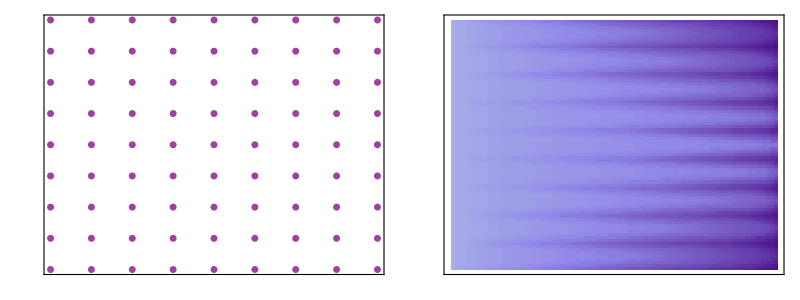

```mathematica
citiesSqrt=Range[0,citiesNumber[[1]],citiesNumber[[2]]];
sampledCoordinates=Tuples[citiesSqrt,2];
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
euclideanDistances=CalculateEuclideanDistances[sampledCoordinates];
(**)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clusteredCoordinates])]]//Flatten//RandomSample;
gridCoordinatesPlot=ListPlot[clusteredCoordinates//Flatten[#,1]&
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,GridLines->None
,GridLinesStyle->Directive[Gray,Opacity[.5],Dashed]
,ImageSize->250
,PlotRangePadding->.5
,PlotStyle->Directive[Purple,EdgeStyle[Black],Opacity[.75],PointSize[.02]]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,FrameTicksStyle->15
];
matrixDistancesPlot=MatrixPlot[Sort/@euclideanDistances,PlotTheme->"LakeMatrixPlot"];
Grid[{{gridCoordinatesPlot,matrixDistancesPlot}}]
```

Movement Kernel

### Inverse-Linear Kernel

```mathematica
(*migrationProbabilities=CalculateInverseLinearKernelMigrationProbabilities[euclideanDistances,0];
(**)
matrixMigrationPlot=MatrixPlot[Sort/@migrationProbabilities,PlotTheme->"LakeMatrixPlot"];
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
originalMap=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,edgeChopThreshold],.1,
(#->.5)&/@(ToString/@Range[migrationProbabilities//Length]),
stylesListType
];*)
```

### Exponential Kernel

```mathematica
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
(**)
matrixMigrationPlot=MatrixPlot[Sort/@migrationProbabilities,PlotTheme->"LakeMatrixPlot"];
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
originalMap=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,.05*edgeChopThreshold],.1,
(#->.5)&/@(ToString/@Range[migrationProbabilities//Length]),
stylesListType
];
```

Markov Baseline

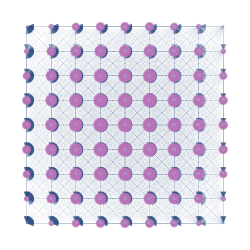

```mathematica
baselineMarkovSS=CalculateMarkovSteadyState[migrationProbabilities];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
markovBaseline=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,.05*edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[.5+7.5*Rescale[baselineMarkovSS]]],
stylesListType
]
```

## Network Dimensionality

Dimension

```mathematica
cityType=RandomChoice[Range[networkDimension],sampledCoordinates//Length]
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
(**)
matrixPenalizationsPlot=MatrixPlot[Sort/@dimensionalPenalizationsMask,PlotTheme->"LakeMatrixPlot"];
matrixDimensionalPlot=MatrixPlot[Sort/@migrationDimensionalMatrix,PlotTheme->"LakeMatrixPlot"];
```

{4,3,3,3,3,2,4,2,1,4,1,2,1,1,1,4,4,3,1,2,3,2,3,4,2,4,4,4,4,4,2,3,1,1,4,3,2,2,4,4,2,4,3,2,1,3,1,2,4,3,4,4,4,1,1,4,1,2,4,2,4,1,3,1,4,3,3,4,1,4,1,1,4,3,2,3,1,1,2,4,3}

Markov Dimensional Network

```mathematica
markovPDF=CalculateMarkovSteadyState[migrationDimensionalMatrix];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
markovDimensional=GraphPlotWrapper[
Chop[migrationDimensionalMatrix,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[0+7.5*Rescale[markovPDF]]],
stylesListType
];
```

Markov Dimensional Difference

```mathematica
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
markovDimensionalDifference=GraphPlotWrapper[
Chop[migrationDimensionalMatrix,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[0+7.5*Rescale[Chop[Abs[baselineMarkovSS-markovPDF]]]]],
stylesListType
];
```

```mathematica
distributionOfDifferences=DistributionChart[baselineMarkovSS-markovPDF
,AspectRatio->1/6
,Axes->{False,True}
,AxesOrigin->{0,0}
,AxesStyle->Directive[Thick,Gray,Opacity[.25]]
,BarOrigin->Right
,BarSpacing->0
,ChartStyle->"LakeColors"
,Frame->False
,FrameTicks->None
,FrameStyle->Directive[Gray,Thin]
,GridLines->None
,ImageSize->imageSize
,PlotRange->{All,All}
,PlotRangePadding->0
];
markovDistributions=SmoothHistogram[{baselineMarkovSS,markovPDF}
,Frame->True
,FrameStyle->Directive[Thick,Gray]
,GridLines->Automatic
,PlotRange->{{0,All},{0,All}}
,PlotStyle->Thickness[.01]
,ImageSize->imageSize
,FrameTicks->{Automatic,None}
];
```

## Attractors/Repellents

Attractors

```mathematica
{attractorScaler,attractorCoverage,attractorDimension}={100,.1,2};
attractorDimensionPositions=Position[cityType,attractorDimension];
sampledAttractors=(Position[cityType,attractorDimension]//Flatten//RandomSample)[[1;;Round[attractorCoverage*Length[attractorDimensionPositions]]]]
```

{37,75}

{{0.,0.,0.,0.,0.,0.,0.,0.,0.0131272,0.,0.275503,0.,0.122812,0.0787724,0.0501742,0.,0.,0.,0.210156,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0357735,0.0238491,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00848456,0.,0.0501742,0.,0.,0.,0.,0.,0.,0.00676598,0.0330848,0.,0.0284761,0.,0.,0.,0.,0.00747092,0.,0.0208401,0.,0.,0.,0.,0.00993728,0.,0.00545618,0.00389248,0.,0.,0.,0.,0.00848456,0.00676598,0.,0.,0.},{0.19794,0.,0.,0.,0.,0.,0.0311616,0.,0.,0.163452,0.,0.,0.,0.,0.,0.0297676,0.018892,0.,0.,0.,0.,0.,0.,0.039772,0.,0.0168945,0.0108627,0.0728624,0.0785375,0.0728624,0.,0.,0.,0.,0.0141493,0.,0.,0.,0.0467345,0.039772,0.,0.0230023,0.,0.,0.,0.,0.,0.,0.0260799,0.,0.016292,0.0119646,0.00850204,0.,0.,0.0196287,0.,0.,0.0141493,0.,0.00850204,0.,0.,0.,0.0123641,0.,0.,0.00930165,0.,0.00589564,0.,0.,0.00756725,0.,0.,0.,0.,0.,0.,0.00309014,0.},{0.125719,0.,0.,0.,0.,0.,0.0498822,0.,0.,0.112724,0.,0.,0.,0.,0.,0.0471232,0.0300152,0.,0.,0.,0.,0.,0.,0.0598581,0.,0.0262968,0.017035,0.0598581,0.0734683,0.0791907,0.,0.,0.,0.,0.0214004,0.,0.,0.,0.0498822,0.0471232,0.,0.0314208,0.,0.,0.,0.,0.,0.,0.0300152,0.,0.0214004,0.0164275,0.0120641,0.,0.,0.0190492,0.,0.,0.017035,0.,0.011308,0.,0.,0.,0.0120641,0.,0.,0.010953,0.,0.00763018,0.,0.,0.00700826,0.,0.,0.,0.,0.,0.,0.00404754,0.},{0.0761091,0.,0.,0.,0.,0.,0.0761091,0.,0.,0.0706095,0.,0.,0.,0.,0.,0.0706095,0.0452895,0.,0.,0.,0.,0.,0.,0.0823904,0.,0.0385423,0.0252736,0.0428552,0.0575288,0.0706095,0.,0.,0.,0.,0.0301981,0.,0.,0.,0.0452895,0.0479411,0.,0.0385423,0.,0.,0.,0.,0.,0.,0.0301981,0.,0.0252736,0.0205676,0.0157882,0.,0.,0.0163721,0.,0.,0.0183079,0.,0.0137118,0.,0.,0.,0.0105268,0.,0.,0.0115947,0.,0.00901405,0.,0.,0.00586945,0.,0.,0.,0.,0.,0.,0.00487812,0.},{0.0437865,0.,0.,0.,0.,0.,0.110356,0.,0.,0.0413647,0.,0.,0.,0.,0.,0.098949,0.0644904,0.,0.,0.,0.,0.,0.,0.098949,0.,0.0525433,0.0352021,0.0275811,0.0391413,0.0525433,0.,0.,0.,0.,0.0391413,0.,0.,0.,0.0352021,0.0413647,0.,0.0413647,0.,0.,0.,0.,0.,0.,0.0263473,0.,0.0263473,0.0230833,0.0187852,0.,0.,0.0125235,0.,0.,0.0173733,0.,0.0149533,0.,0.,0.,0.00823288,0.,0.,0.0109435,0.,0.00961455,0.,0.,0.00445538,0.,0.,0.,0.,0.,0.,0.0053608,0.},{0.,0.0519346,0.082449,0.130892,0.207798,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0764913,0.,0.,0.062321,0.,0.117362,0.,0.,0.,0.,0.,0.,0.,0.,0.0764913,0.,0.,0.,0.046425,0.,0.,0.,0.,0.,0.,0.0490621,0.,0.,0.0125605,0.,0.,0.,0.0312502,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.014854,0.,0.,0.00976492,0.0114037,0.,0.,0.,0.,0.,0.,0.00528447,0.,0.00729662,0.,0.,0.,0.,0.00635838},{0.,0.,0.,0.,0.,0.,0.,0.,0.148654,0.,0.0354908,0.,0.0868711,0.133288,0.194877,0.,0.,0.,0.0201426,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0868711,0.0936373,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0474187,0.,0.0142649,0.,0.,0.,0.,0.,0.,0.0310941,0.00741988,0.,0.0133709,0.,0.,0.,0.,0.0225243,0.,0.00528457,0.,0.,0.,0.,0.0142649,0.,0.0142649,0.0129512,0.,0.,0.,0.,0.00828677,0.00902215,0.,0.,0.},{0.,0.0294425,0.0467415,0.0742047,0.117804,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.245173,0.,0.,0.0391192,0.,0.0890448,0.,0.,0.,0.,0.,0.,0.,0.,0.0663325,0.,0.,0.,0.109291,0.,0.,0.,0.,0.,0.,0.0701004,0.,0.,0.00884329,0.,0.,0.,0.0318352,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0283375,0.,0.,0.00884329,0.0113507,0.,0.,0.,0.,0.,0.,0.00463512,0.,0.0075505,0.,0.,0.,0.,0.0113507},{0.,0.,0.,0.,0.,0.139725,0.,0.352152,0.,0.,0.,0.0336105,0.,0.,0.,0.,0.,0.,0.,0.0193256,0.,0.0463984,0.,0.,0.151256,0.,0.,0.,0.,0.,0.037759,0.,0.,0.,0.,0.,0.904504,0.0134628,0.,0.,0.040923,0.,0.,0.0831446,0.,0.,0.,0.0151258,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0151258,0.,0.0251728,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.555259,0.,0.,0.,0.0123654,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00975576,0.,0.255186,0.,0.101251,0.0637781,0.0401738,0.,0.,0.,0.255186,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0336225,0.0217805,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00780838,0.,0.0602505,0.,0.,0.,0.,0.,0.,0.00648957,0.0401738,0.,0.0336225,0.,0.,0.,0.,0.00760071,0.,0.0253055,0.,0.,0.,0.,0.0109609,0.,0.00571427,0.00398383,0.,0.,0.,0.,0.00975576,0.00760071,0.,0.,0.},{0.,0.,0.,0.,0.,0.0465101,0.,0.0188013,0.,0.,0.,0.196989,0.,0.,0.,0.,0.,0.,0.,0.196989,0.,0.111257,0.,0.,0.0296246,0.,0.,0.,0.,0.,0.0846108,0.,0.,0.,0.,0.,7.32375,0.0781603,0.,0.,0.0440101,0.,0.,0.0140813,0.,0.,0.,0.0465101,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0259547,0.,0.0162137,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.20262,0.,0.,0.,0.00586733,0.,0.},{0.,0.130344,0.157846,0.130344,0.0891499,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0156528,0.,0.,0.157846,0.,0.0891499,0.,0.,0.,0.,0.,0.,0.,0.,0.0677981,0.,0.,0.,0.0134724,0.,0.,0.,0.,0.,0.,0.0248497,0.,0.,0.031716,0.,0.,0.,0.031716,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00677991,0.,0.,0.0156528,0.0150654,0.,0.,0.,0.,0.,0.,0.00954111,0.,0.00954111,0.,0.,0.,0.,0.00353459},{0.,0.,0.,0.,0.,0.0934265,0.,0.039056,0.,0.,0.,0.165419,0.,0.,0.,0.,0.,0.,0.,0.0934265,0.,0.165419,0.,0.,0.0608911,0.,0.,0.,0.,0.,0.104197,0.,0.,0.,0.,0.,3.73264,0.0496108,0.,0.,0.0608911,0.,0.,0.0260418,0.,0.,0.,0.039056,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0260418,0.,0.021795,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.00988,0.,0.,0.,0.00777339,0.,0.},{0.,0.,0.,0.,0.,0.143369,0.,0.0639101,0.,0.,0.,0.109363,0.,0.,0.,0.,0.,0.,0.,0.0639101,0.,0.143369,0.,0.,0.0980587,0.,0.,0.,0.,0.,0.0980587,0.,0.,0.,0.,0.,2.76063,0.0387891,0.,0.,0.0688879,0.,0.,0.0387891,0.,0.,0.,0.0348854,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0261102,0.,0.0261102,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.962332,0.,0.,0.,0.00952804,0.,0.},{0.,0.,0.,0.,0.,0.181671,0.,0.102606,0.,0.,0.,0.0720823,0.,0.,0.,0.,0.,0.,0.,0.0428933,0.,0.102606,0.,0.,0.150017,0.,0.,0.,0.,0.,0.0780312,0.,0.,0.,0.,0.,1.96742,0.0286004,0.,0.,0.0668736,0.,0.,0.054485,0.,0.,0.,0.0286004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0239364,0.,0.0286004,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.86225,0.,0.,0.,0.0109812,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.106147,0.,0.0295875,0.,0.0745701,0.118384,0.187941,0.,0.,0.,0.0179377,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.106147,0.118384,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0563655,0.,0.0154689,0.,0.,0.,0.,0.,0.,0.0377629,0.00807255,0.,0.0154689,0.,0.,0.,0.,0.0282639,0.,0.00590898,0.,0.,0.,0.,0.0179377,0.,0.0179377,0.016041,0.,0.,0.,0.,0.0103139,0.0113602,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.18073,0.,0.0217037,0.,0.0547004,0.0868398,0.137863,0.,0.,0.,0.0132294,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0940067,0.123612,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0805648,0.,0.0124003,0.,0.,0.,0.,0.,0.,0.0516749,0.00651888,0.,0.0132294,0.,0.,0.,0.,0.0344558,0.,0.00490094,0.,0.,0.,0.,0.0186804,0.,0.0217037,0.0208892,0.,0.,0.,0.,0.010285,0.012011,0.,0.,0.},{0.00565071,0.,0.,0.,0.,0.,0.0834805,0.,0.,0.00581567,0.,0.,0.,0.,0.,0.0931045,0.147808,0.,0.,0.,0.,0.,0.,0.0544087,0.,0.122055,0.147808,0.00519013,0.00811152,0.0126156,0.,0.,0.,0.,0.0834805,0.,0.,0.,0.0105657,0.0158486,0.,0.0330224,0.,0.,0.,0.,0.,0.,0.0121657,0.,0.0232694,0.0296991,0.0348982,0.,0.,0.00440247,0.,0.,0.0121657,0.,0.0194747,0.,0.,0.,0.00330981,0.,0.,0.00837441,0.,0.0126156,0.,0.,0.00172447,0.,0.,0.,0.,0.,0.,0.00893435,0.},{0.,0.,0.,0.,0.,0.0279004,0.,0.0116209,0.,0.,0.,0.119598,0.,0.,0.,0.,0.,0.,0.,0.211757,0.,0.0840195,0.,0.,0.0209988,0.,0.,0.,0.,0.,0.0779483,0.,0.,0.,0.,0.,13.4719,0.119598,0.,0.,0.0425481,0.,0.,0.0116209,0.,0.,0.,0.0635081,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0333368,0.,0.0174292,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.82545,0.,0.,0.,0.00665776,0.,0.},{0.,0.124475,0.111609,0.0848778,0.0592657,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0119447,0.,0.,0.197611,0.,0.078407,0.,0.,0.,0.,0.,0.,0.,0.,0.0727413,0.,0.,0.,0.0119447,0.,0.,0.,0.,0.,0.,0.0260366,0.,0.,0.0727413,0.,0.,0.,0.044149,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00755467,0.,0.,0.0297182,0.0260366,0.,0.,0.,0.,0.,0.,0.0195961,0.,0.0168664,0.,0.,0.,0.,0.00442502},{0.0525547,0.,0.,0.,0.,0.,0.0245851,0.,0.,0.0691059,0.,0.,0.,0.,0.,0.028889,0.0184009,0.,0.,0.,0.,0.,0.,0.0485481,0.,0.0192626,0.0121335,0.0691059,0.101038,0.122357,0.,0.,0.,0.,0.0184009,0.,0.,0.,0.0770727,0.0691059,0.,0.0366962,0.,0.,0.,0.,0.,0.,0.04504,0.,0.0273362,0.0192626,0.0131196,0.,0.,0.028889,0.,0.,0.0245851,0.,0.0142189,0.,0.,0.,0.0184009,0.,0.,0.0161214,0.,0.0100709,0.,0.,0.0104433,0.,0.,0.,0.,0.,0.,0.00525555,0.},{0.,0.0629373,0.0827583,0.0922991,0.0827583,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0220362,0.,0.,0.14653,0.,0.14653,0.,0.,0.,0.,0.,0.,0.,0.,0.120999,0.,0.,0.,0.0220362,0.,0.,0.,0.,0.,0.,0.0439458,0.,0.,0.0327368,0.,0.,0.,0.053938,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0120605,0.,0.,0.0220362,0.0230681,0.,0.,0.,0.,0.,0.,0.0125065,0.,0.0145306,0.,0.,0.,0.,0.00629383},{0.0224886,0.,0.,0.,0.,0.,0.0480731,0.,0.,0.0264255,0.,0.,0.,0.,0.,0.0632129,0.0411992,0.,0.,0.,0.,0.,0.,0.111923,0.,0.0444082,0.0279727,0.0264255,0.0411992,0.0632129,0.,0.,0.,0.,0.0411992,0.,0.,0.,0.0480731,0.0632129,0.,0.0632129,0.,0.,0.,0.,0.,0.,0.0411992,0.,0.0411992,0.0335669,0.0250051,0.,0.,0.01762,0.,0.,0.0279727,0.,0.0224886,0.,0.,0.,0.0120008,0.,0.,0.01762,0.,0.0147466,0.,0.,0.00634125,0.,0.,0.,0.,0.,0.,0.00800057,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.044879,0.,0.035331,0.,0.0845158,0.123568,0.149641,0.,0.,0.,0.023558,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.149641,0.123568,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.044879,0.,0.023558,0.,0.,0.,0.,0.,0.,0.0334319,0.0123166,0.,0.023558,0.,0.,0.,0.,0.0300674,0.,0.00904515,0.,0.,0.,0.,0.023558,0.,0.0197163,0.0160451,0.,0.,0.,0.,0.0142823,0.0148392,0.,0.,0.},{0.,0.0252028,0.0384344,0.0573679,0.0821598,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.108035,0.,0.,0.047807,0.,0.120489,0.,0.,0.,0.,0.,0.,0.,0.,0.108035,0.,0.,0.,0.108035,0.,0.,0.,0.,0.,0.,0.120489,0.,0.,0.0136734,0.,0.,0.,0.0573679,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0384344,0.,0.,0.015744,0.0205101,0.,0.,0.,0.,0.,0.,0.00821611,0.,0.0136734,0.,0.,0.,0.,0.0163263},{0.,0.,0.,0.,0.,0.,0.,0.,0.106901,0.,0.0180652,0.,0.044689,0.0696733,0.106901,0.,0.,0.,0.011823,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.106901,0.156298,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.106901,0.,0.01353,0.,0.,0.,0.,0.,0.,0.0696733,0.00723604,0.,0.0155789,0.,0.,0.,0.,0.0473055,0.,0.0056376,0.,0.,0.,0.,0.0249385,0.,0.0297977,0.0284647,0.,0.,0.,0.,0.01353,0.016155,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.14406,0.,0.013824,0.,0.0343939,0.0539976,0.084186,0.,0.,0.,0.00899853,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.084186,0.129168,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.14406,0.,0.0107472,0.,0.,0.,0.,0.,0.,0.0907431,0.00581607,0.,0.0129576,0.,0.,0.,0.,0.0539976,0.,0.004638,0.,0.,0.,0.,0.0245223,0.,0.0343939,0.0360045,0.,0.,0.,0.,0.0129576,0.0163483,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00694632,0.,0.128214,0.,0.0680836,0.0456136,0.0299105,0.,0.,0.,0.227013,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0357385,0.0225117,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0086787,0.,0.128214,0.,0.,0.,0.,0.,0.,0.00797131,0.0900728,0.,0.0680836,0.,0.,0.,0.,0.0106678,0.,0.0567368,0.,0.,0.,0.,0.0186849,0.,0.0086787,0.0057731,0.,0.,0.,0.,0.0186849,0.0137219,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00934237,0.,0.125228,0.,0.0853912,0.0596242,0.0399461,0.,0.,0.,0.164167,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0496873,0.031298,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.012017,0.,0.125228,0.,0.,0.,0.,0.,0.,0.0109102,0.0731813,0.,0.0731813,0.,0.,0.,0.,0.0142112,0.,0.0469391,0.,0.,0.,0.,0.023103,0.,0.0112638,0.00760037,0.,0.,0.,0.,0.0213168,0.0163633,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0131698,0.,0.104055,0.,0.104055,0.0791336,0.0552548,0.,0.,0.,0.104055,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0731006,0.0460461,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0175842,0.,0.104055,0.,0.,0.,0.,0.,0.,0.0157249,0.0552548,0.,0.0731006,0.,0.,0.,0.,0.0197546,0.,0.0370187,0.,0.,0.,0.,0.0290044,0.,0.0151641,0.0104384,0.,0.,0.,0.,0.0242745,0.0197546,0.,0.,0.},{0.,0.0457928,0.056205,0.0605827,0.056205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0201177,0.,0.,0.126084,0.,0.126084,0.,0.,0.,0.,0.,0.,0.,0.,0.152688,0.,0.,0.,0.0240376,0.,0.,0.,0.,0.,0.,0.056205,0.,0.,0.0457928,0.,0.,0.,0.0862366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0163718,0.,0.,0.0360504,0.038161,0.,0.,0.,0.,0.,0.,0.0201177,0.,0.0240376,0.,0.,0.,0.,0.00922932},{0.0153078,0.,0.,0.,0.,0.,0.029162,0.,0.,0.0195375,0.,0.,0.,0.,0.,0.0417646,0.029162,0.,0.,0.,0.,0.,0.,0.0802937,0.,0.0357928,0.0229578,0.0243019,0.0385806,0.0612488,0.,0.,0.,0.,0.0385806,0.,0.,0.,0.0549176,0.0802937,0.,0.0802937,0.,0.,0.,0.,0.,0.,0.0549176,0.,0.0549176,0.0417646,0.029162,0.,0.,0.0217238,0.,0.,0.0385806,0.,0.029162,0.,0.,0.,0.0153078,0.,0.,0.0243019,0.,0.0195375,0.,0.,0.00800323,0.,0.,0.,0.,0.,0.,0.010426,0.},{0.,0.,0.,0.,0.,0.0631363,0.,0.047723,0.,0.,0.,0.047723,0.,0.,0.,0.,0.,0.,0.,0.0375699,0.,0.0898715,0.,0.,0.131399,0.,0.,0.,0.,0.,0.100232,0.,0.,0.,0.,0.,2.41695,0.0375699,0.,0.,0.131399,0.,0.,0.0898715,0.,0.,0.,0.047723,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.047723,0.,0.0631363,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.72325,0.,0.,0.,0.0239302,0.,0.},{0.,0.,0.,0.,0.,0.0666737,0.,0.0666737,0.,0.,0.,0.0363939,0.,0.,0.,0.,0.,0.,0.,0.0272393,0.,0.0666737,0.,0.,0.181128,0.,0.,0.,0.,0.,0.0718668,0.,0.,0.,0.,0.,1.74603,0.0272393,0.,0.,0.102299,0.,0.,0.149569,0.,0.,0.,0.0363939,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0404664,0.,0.0666737,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.50573,0.,0.,0.,0.0285149,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0606908,0.,0.0140723,0.,0.0331281,0.0494476,0.0708167,0.,0.,0.,0.00996592,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.103854,0.164874,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.136147,0.,0.0140723,0.,0.,0.,0.,0.,0.,0.0931192,0.00774782,0.,0.0176784,0.,0.,0.,0.,0.0654179,0.,0.00630315,0.,0.,0.,0.,0.0331281,0.,0.0412067,0.0389275,0.,0.,0.,0.,0.0176784,0.0217233,0.,0.,0.},{0.00391036,0.,0.,0.,0.,0.,0.038327,0.,0.,0.00448738,0.,0.,0.,0.,0.,0.0548903,0.072177,0.,0.,0.,0.,0.,0.,0.0470416,0.,0.105528,0.127795,0.00502822,0.00798257,0.0126728,0.,0.,0.,0.,0.127795,0.,0.,0.,0.0121971,0.0192187,0.,0.0470416,0.,0.,0.,0.,0.,0.,0.0168378,0.,0.038327,0.0548903,0.072177,0.,0.,0.00600536,0.,0.,0.0201187,0.,0.038327,0.,0.,0.,0.00488559,0.,0.,0.0148508,0.,0.0256777,0.,0.,0.00259163,0.,0.,0.,0.,0.,0.,0.0192187,0.},{0.,0.0596415,0.0507561,0.0397677,0.029355,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00772945,0.,0.,0.108499,0.,0.0507561,0.,0.,0.,0.,0.,0.,0.,0.,0.0596415,0.,0.,0.,0.00965715,0.,0.,0.,0.,0.,0.,0.0250497,0.,0.,0.252607,0.,0.,0.,0.0596415,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00887001,0.,0.,0.0757594,0.0564358,0.,0.,0.,0.,0.,0.,0.0596415,0.,0.0397677,0.,0.,0.,0.,0.00642397},{0.,0.0526396,0.0497281,0.0423196,0.0331577,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00989747,0.,0.,0.118955,0.,0.0631669,0.,0.,0.,0.,0.,0.,0.,0.,0.0775295,0.,0.,0.,0.012731,0.,0.,0.,0.,0.,0.,0.0331577,0.,0.,0.173922,0.,0.,0.,0.0775295,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0115585,0.,0.,0.0775295,0.0631669,0.,0.,0.,0.,0.,0.,0.0526396,0.,0.0423196,0.,0.,0.,0.,0.00805197},{0.,0.,0.,0.,0.,0.,0.,0.,0.010078,0.,0.0654772,0.,0.0654772,0.0533473,0.0397402,0.,0.,0.,0.0764018,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0654772,0.0419976,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0176392,0.,0.146885,0.,0.,0.,0.,0.,0.,0.0169772,0.0764018,0.,0.112045,0.,0.,0.,0.,0.0234365,0.,0.0533473,0.,0.,0.,0.,0.0397402,0.,0.0190727,0.0127152,0.,0.,0.,0.,0.0357408,0.0280032,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0140864,0.,0.0513277,0.,0.0679052,0.0629984,0.0513277,0.,0.,0.,0.0513277,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0966599,0.0629984,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.026943,0.,0.0966599,0.,0.,0.,0.,0.,0.,0.0257377,0.0513277,0.,0.0966599,0.,0.,0.,0.,0.0343878,0.,0.0382358,0.,0.,0.,0.,0.0513277,0.,0.026943,0.0183506,0.,0.,0.,0.,0.0404077,0.0343878,0.,0.,0.},{0.,0.0240643,0.0307136,0.0360904,0.0382034,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0240643,0.,0.,0.0656553,0.,0.096285,0.,0.,0.,0.,0.,0.,0.,0.,0.152858,0.,0.,0.,0.0360904,0.,0.,0.,0.,0.,0.,0.096285,0.,0.,0.0360904,0.,0.,0.,0.152858,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0307136,0.,0.,0.0458436,0.0562674,0.,0.,0.,0.,0.,0.,0.0240643,0.,0.0360904,0.,0.,0.,0.,0.0177633},{0.,0.,0.,0.,0.,0.,0.,0.,0.0234525,0.,0.0234525,0.,0.0446782,0.0548369,0.0591081,0.,0.,0.,0.019628,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.148972,0.123015,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0591081,0.,0.0351728,0.,0.,0.,0.,0.,0.,0.0548369,0.019628,0.,0.0446782,0.,0.,0.,0.,0.0639862,0.,0.0159733,0.,0.,0.,0.,0.0591081,0.,0.0446782,0.0332823,0.,0.,0.,0.,0.0351728,0.0372322,0.,0.,0.},{0.00516761,0.,0.,0.,0.,0.,0.0227955,0.,0.,0.00651982,0.,0.,0.,0.,0.,0.0361891,0.033574,0.,0.,0.,0.,0.,0.,0.0515134,0.,0.0515134,0.0391757,0.00870521,0.0137165,0.0215347,0.,0.,0.,0.,0.0753164,0.,0.,0.,0.0227955,0.0361891,0.,0.0912083,0.,0.,0.,0.,0.,0.,0.033574,0.,0.0753164,0.0912083,0.0753164,0.,0.,0.0120173,0.,0.,0.0391757,0.,0.0574521,0.,0.,0.,0.00977969,0.,0.,0.0273543,0.,0.0361891,0.,0.,0.00516761,0.,0.,0.,0.,0.,0.,0.0215347,0.},{0.,0.0111679,0.016224,0.0229063,0.0310316,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0725584,0.,0.,0.0259711,0.,0.0591167,0.,0.,0.,0.,0.,0.,0.,0.,0.0725584,0.,0.,0.,0.16277,0.,0.,0.,0.,0.,0.,0.197114,0.,0.,0.0119147,0.,0.,0.,0.0725584,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.111328,0.,0.,0.0211353,0.0310316,0.,0.,0.,0.,0.,0.,0.0111679,0.,0.0229063,0.,0.,0.,0.,0.0465395},{0.,0.,0.,0.,0.,0.0467428,0.,0.0701024,0.,0.,0.,0.0212241,0.,0.,0.,0.,0.,0.,0.,0.0162942,0.,0.0391202,0.,0.,0.12753,0.,0.,0.,0.,0.,0.0446518,0.,0.,0.,0.,0.,1.17992,0.0185463,0.,0.,0.0742068,0.,0.,0.296913,0.,0.,0.,0.0283383,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0391202,0.,0.0890473,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.69905,0.,0.,0.,0.0596585,0.,0.},{0.0236368,0.,0.,0.,0.,0.,0.00644899,0.,0.,0.0375247,0.,0.,0.,0.,0.,0.00850663,0.00573993,0.,0.,0.,0.,0.,0.,0.0160988,0.,0.00705552,0.00459417,0.0945745,0.0847986,0.0644889,0.,0.,0.,0.,0.0082396,0.,0.,0.,0.0847986,0.0552678,0.,0.0225794,0.,0.,0.,0.,0.,0.,0.0595725,0.,0.0236368,0.0148888,0.00937847,0.,0.,0.123982,0.,0.,0.0354492,0.,0.01433,0.,0.,0.,0.0847986,0.,0.,0.030168,0.,0.0128148,0.,0.,0.0595725,0.,0.,0.,0.,0.,0.,0.00705552,0.},{0.,0.,0.,0.,0.,0.0133609,0.,0.00697246,0.,0.,0.,0.0383266,0.,0.,0.,0.,0.,0.,0.,0.064408,0.,0.0486842,0.,0.,0.0174055,0.,0.,0.,0.,0.,0.0697235,0.,0.,0.,0.,0.,13.5386,0.162329,0.,0.,0.0597539,0.,0.,0.0154932,0.,0.,0.,0.162329,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0916817,0.,0.0383266,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.03514,0.,0.,0.,0.0174055,0.,0.},{0.,0.0275843,0.0288761,0.0275843,0.0241671,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0103922,0.,0.,0.0727772,0.,0.0550103,0.,0.,0.,0.,0.,0.,0.,0.,0.0787835,0.,0.,0.,0.0156553,0.,0.,0.,0.,0.,0.,0.0433068,0.,0.,0.115538,0.,0.,0.,0.115538,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0175064,0.,0.,0.115538,0.103595,0.,0.,0.,0.,0.,0.,0.0675183,0.,0.0675183,0.,0.,0.,0.,0.0131115},{0.,0.,0.,0.,0.,0.,0.,0.,0.0100759,0.,0.0334938,0.,0.0416616,0.0393573,0.0334938,0.,0.,0.,0.0372418,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0715985,0.0499935,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0250687,0.,0.105001,0.,0.,0.,0.,0.,0.,0.0262426,0.0613608,0.,0.13765,0.,0.,0.,0.,0.0393573,0.,0.0499935,0.,0.,0.,0.,0.0715985,0.,0.0334938,0.0219631,0.,0.,0.,0.,0.0613608,0.0499935,0.,0.,0.},{0.00710534,0.,0.,0.,0.,0.,0.0113741,0.,0.,0.0100319,0.,0.,0.,0.,0.,0.0173456,0.0135904,0.,0.,0.,0.,0.,0.,0.0317771,0.,0.0192866,0.0135904,0.0173456,0.0258903,0.037079,0.,0.,0.,0.,0.0258903,0.,0.,0.,0.0487563,0.0712854,0.,0.0712854,0.,0.,0.,0.,0.,0.,0.0863267,0.,0.0863267,0.0543772,0.0342522,0.,0.,0.0317771,0.,0.,0.0863267,0.,0.0487563,0.,0.,0.,0.0258903,0.,0.,0.0543772,0.,0.037079,0.,0.,0.0135904,0.,0.,0.,0.,0.,0.,0.0192866,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0163293,0.,0.0176975,0.,0.0305999,0.0359567,0.0380619,0.,0.,0.,0.0163293,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0959284,0.0860125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.056059,0.,0.0380619,0.,0.,0.,0.,0.,0.,0.0604253,0.0229027,0.,0.056059,0.,0.,0.,0.,0.0860125,0.,0.0200654,0.,0.,0.,0.,0.0959284,0.,0.0654122,0.0456738,0.,0.,0.,0.,0.056059,0.0604253,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0191046,0.,0.0119345,0.,0.0228272,0.0291346,0.0342349,0.,0.,0.,0.0103649,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0818939,0.091335,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0818939,0.,0.0228272,0.,0.,0.,0.,0.,0.,0.091335,0.0138392,0.,0.0342349,0.,0.,0.,0.,0.119735,0.,0.0123759,0.,0.,0.,0.,0.0818939,0.,0.0818939,0.06228,0.,0.,0.,0.,0.0434868,0.0533746,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.021298,0.,0.00802387,0.,0.0164576,0.0222954,0.0284559,0.,0.,0.,0.00665511,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0608291,0.0799861,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.116946,0.,0.0140439,0.,0.,0.,0.,0.,0.,0.141621,0.00856038,0.,0.021298,0.,0.,0.,0.,0.141621,0.,0.00777199,0.,0.,0.,0.,0.0608291,0.,0.0892073,0.0799861,0.,0.,0.,0.,0.0316401,0.0424737,0.,0.,0.},{0.,0.,0.,0.,0.,0.0351583,0.,0.0493114,0.,0.,0.,0.0185777,0.,0.,0.,0.,0.,0.,0.,0.0154086,0.,0.0351583,0.,0.,0.0983396,0.,0.,0.,0.,0.,0.0432026,0.,0.,0.,0.,0.,1.26608,0.0198199,0.,0.,0.0774178,0.,0.,0.270765,0.,0.,0.,0.0325158,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0493114,0.,0.1207,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.36733,0.,0.,0.,0.0983396,0.,0.},{0.,0.,0.,0.,0.,0.0108601,0.,0.00566174,0.,0.,0.,0.0333134,0.,0.,0.,0.,0.,0.,0.,0.0596967,0.,0.0398045,0.,0.,0.0143252,0.,0.,0.,0.,0.,0.056488,0.,0.,0.,0.,0.,16.0857,0.142801,0.,0.,0.0508031,0.,0.,0.0138755,0.,0.,0.,0.142801,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.10032,0.,0.0398045,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,10.9686,0.,0.,0.,0.0215803,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.003773,0.,0.0265258,0.,0.0222001,0.0180665,0.0138683,0.,0.,0.,0.039782,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0265258,0.0180665,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00924669,0.,0.168493,0.,0.,0.,0.,0.,0.,0.0101847,0.168493,0.,0.168493,0.,0.,0.,0.,0.0167086,0.,0.139136,0.,0.,0.,0.,0.039782,0.,0.0160815,0.0101847,0.,0.,0.,0.,0.0505329,0.0338553,0.,0.,0.},{0.,0.,0.,0.,0.,0.0118909,0.,0.00714498,0.,0.,0.,0.0261878,0.,0.,0.,0.,0.,0.,0.,0.039275,0.,0.039275,0.,0.,0.0193308,0.,0.,0.,0.,0.,0.0612324,0.,0.,0.,0.,0.,7.21632,0.0939503,0.,0.,0.0714487,0.,0.,0.0219172,0.,0.,0.,0.166346,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.166346,0.,0.0660017,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,10.5829,0.,0.,0.,0.0334238,0.,0.},{0.,0.0141041,0.0157718,0.0163867,0.0157718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00998847,0.,0.,0.0390156,0.,0.0390156,0.,0.,0.,0.,0.,0.,0.,0.,0.0608281,0.,0.,0.,0.0177184,0.,0.,0.,0.,0.,0.,0.0495595,0.,0.,0.0608281,0.,0.,0.,0.136455,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0260148,0.,0.,0.136455,0.165247,0.,0.,0.,0.,0.,0.,0.070977,0.,0.104089,0.,0.,0.,0.,0.0217725},{0.,0.,0.,0.,0.,0.,0.,0.,0.00892407,0.,0.0168888,0.,0.0236874,0.0247967,0.0236874,0.,0.,0.,0.0183039,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0579799,0.0472389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0316484,0.,0.0579799,0.,0.,0.,0.,0.,0.,0.0371888,0.0393661,0.,0.0992155,0.,0.,0.,0.,0.0624958,0.,0.0371888,0.,0.,0.,0.,0.130066,0.,0.0579799,0.0371888,0.,0.,0.,0.,0.0992155,0.0889598,0.,0.,0.},{0.,0.0108911,0.0137409,0.0164069,0.0183468,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0206113,0.,0.,0.0302623,0.,0.0453857,0.,0.,0.,0.,0.,0.,0.,0.,0.0707595,0.,0.,0.,0.0429462,0.,0.,0.,0.,0.,0.,0.108568,0.,0.,0.0289085,0.,0.,0.,0.158734,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0762708,0.,0.,0.0707595,0.108568,0.,0.,0.,0.,0.,0.,0.0386241,0.,0.0825654,0.,0.,0.,0.,0.057651},{0.,0.,0.,0.,0.,0.,0.,0.,0.0119263,0.,0.00844618,0.,0.0149826,0.0184106,0.0210139,0.,0.,0.,0.00791683,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0514358,0.055442,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0600176,0.,0.0210139,0.,0.,0.,0.,0.,0.,0.0789191,0.0138565,0.,0.0349229,0.,0.,0.,0.,0.139732,0.,0.0133365,0.,0.,0.,0.,0.115386,0.,0.115386,0.0789191,0.,0.,0.,0.,0.0600176,0.0789191,0.,0.,0.},{0.,0.,0.,0.,0.,0.0236551,0.,0.0274835,0.,0.,0.,0.0167524,0.,0.,0.,0.,0.,0.,0.,0.0157025,0.,0.0322071,0.,0.,0.0654362,0.,0.,0.,0.,0.,0.0436315,0.,0.,0.,0.,0.,1.53617,0.0236551,0.,0.,0.08312,0.,0.,0.174576,0.,0.,0.,0.0416797,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0692674,0.,0.174576,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.68815,0.,0.,0.,0.156531,0.,0.},{0.00244173,0.,0.,0.,0.,0.,0.0133495,0.,0.,0.00317186,0.,0.,0.,0.,0.,0.0206075,0.0235214,0.,0.,0.,0.,0.,0.,0.0246229,0.,0.0369281,0.0390902,0.00478583,0.00734987,0.0111803,0.,0.,0.,0.,0.0575735,0.,0.,0.,0.0133495,0.0206075,0.,0.0469078,0.,0.,0.,0.,0.,0.,0.0235214,0.,0.0575735,0.0883363,0.129154,0.,0.,0.00976973,0.,0.,0.0390902,0.,0.0985201,0.,0.,0.,0.00945404,0.,0.,0.0369281,0.,0.0883363,0.,0.,0.00549203,0.,0.,0.,0.,0.,0.,0.0883363,0.},{0.,0.,0.,0.,0.,0.00940472,0.,0.00516377,0.,0.,0.,0.02695,0.,0.,0.,0.,0.,0.,0.,0.0474853,0.,0.0338563,0.,0.,0.0135624,0.,0.,0.,0.,0.,0.049709,0.,0.,0.,0.,0.,12.6536,0.11623,0.,0.,0.049709,0.,0.,0.014838,0.,0.,0.,0.135622,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.11623,0.,0.0474853,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,18.0118,0.,0.,0.,0.0301366,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00316173,0.,0.0191719,0.,0.0165013,0.01382,0.0109537,0.,0.,0.,0.0290748,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0224669,0.0159128,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00908516,0.,0.121781,0.,0.,0.,0.,0.,0.,0.0106099,0.159647,0.,0.159647,0.,0.,0.,0.,0.0184523,0.,0.193333,0.,0.,0.,0.,0.0483194,0.,0.0191719,0.0120764,0.,0.,0.,0.,0.0711665,0.0456468,0.,0.,0.},{0.00715937,0.,0.,0.,0.,0.,0.00498741,0.,0.,0.0111348,0.,0.,0.,0.,0.,0.00739139,0.00560351,0.,0.,0.,0.,0.,0.,0.0139882,0.,0.00788561,0.00560351,0.0262129,0.0308017,0.0326051,0.,0.,0.,0.,0.0107377,0.,0.,0.,0.0517624,0.048022,0.,0.0291461,0.,0.,0.,0.,0.,0.,0.0736813,0.,0.0391258,0.0262129,0.0171887,0.,0.,0.107727,0.,0.,0.0736813,0.,0.0308017,0.,0.,0.,0.130458,0.,0.,0.0821755,0.,0.0326051,0.,0.,0.0736813,0.,0.,0.,0.,0.,0.,0.0196192,0.},{0.00566624,0.,0.,0.,0.,0.,0.00566624,0.,0.,0.00861926,0.,0.,0.,0.,0.,0.00861926,0.00683163,0.,0.,0.,0.,0.,0.,0.015887,0.,0.00992449,0.00728841,0.0189826,0.0242277,0.028469,0.,0.,0.,0.,0.0140122,0.,0.,0.,0.0443852,0.0478423,0.,0.0361627,0.,0.,0.,0.,0.,0.,0.0759522,0.,0.0517907,0.0361627,0.0242277,0.,0.,0.0681012,0.,0.,0.0995691,0.,0.0443852,0.,0.,0.,0.0759522,0.,0.,0.120578,0.,0.0478423,0.,0.,0.0443852,0.,0.,0.,0.,0.,0.,0.028469,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00590994,0.,0.0110504,0.,0.0147545,0.0153298,0.0147545,0.,0.,0.,0.0127238,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0364991,0.0310615,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0243369,0.,0.0463629,0.,0.,0.,0.,0.,0.,0.0310615,0.0364991,0.,0.0873101,0.,0.,0.,0.,0.0569047,0.,0.0386361,0.,0.,0.,0.,0.154589,0.,0.0613369,0.0386361,0.,0.,0.,0.,0.154589,0.127654,0.,0.,0.},{0.,0.,0.,0.,0.,0.0131629,0.,0.0115645,0.,0.,0.,0.0150635,0.,0.,0.,0.,0.,0.,0.,0.0173446,0.,0.0277649,0.,0.,0.0316909,0.,0.,0.,0.,0.,0.0423416,0.,0.,0.,0.,0.,2.28211,0.0331749,0.,0.,0.0775699,0.,0.,0.0631998,0.,0.,0.,0.0631998,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.119017,0.,0.210729,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.83456,0.,0.,0.,0.174012,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00782058,0.,0.00612104,0.,0.0101868,0.0121632,0.0136013,0.,0.,0.,0.00612104,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0336465,0.0356164,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0427393,0.,0.0187762,0.,0.,0.,0.,0.,0.,0.0612094,0.0136013,0.,0.0336465,0.,0.,0.,0.,0.117677,0.,0.0141317,0.,0.,0.,0.,0.142507,0.,0.142507,0.089765,0.,0.,0.,0.,0.0804863,0.117677,0.,0.,0.},{0.,0.,0.,0.,0.,0.0171517,0.,0.0195223,0.,0.,0.,0.0134243,0.,0.,0.,0.,0.,0.,0.,0.0134243,0.,0.0257242,0.,0.,0.0470016,0.,0.,0.,0.,0.,0.0363195,0.,0.,0.,0.,0.,1.48337,0.0223411,0.,0.,0.0698252,0.,0.,0.124007,0.,0.,0.,0.041179,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0737915,0.,0.176518,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.74716,0.,0.,0.,0.258082,0.,0.},{0.,0.,0.,0.,0.,0.0203397,0.,0.0261627,0.,0.,0.,0.0136085,0.,0.,0.,0.,0.,0.,0.,0.0128919,0.,0.0261627,0.,0.,0.0570284,0.,0.,0.,0.,0.,0.0356252,0.,0.,0.,0.,0.,1.33765,0.0203397,0.,0.,0.0681404,0.,0.,0.159326,0.,0.,0.,0.0369427,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0650922,0.,0.159326,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.17239,0.,0.,0.,0.244458,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00237518,0.,0.0168778,0.,0.0131213,0.0106747,0.00831664,0.,0.,0.,0.0276891,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0168778,0.0119933,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00710083,0.,0.102783,0.,0.,0.,0.,0.,0.,0.00854387,0.175882,0.,0.119931,0.,0.,0.,0.,0.0153234,0.,0.279223,0.,0.,0.,0.,0.0419914,0.,0.0168778,0.0106747,0.,0.,0.,0.,0.0697855,0.0439579,0.,0.,0.},{0.00676483,0.,0.,0.,0.,0.,0.0035885,0.,0.,0.0106959,0.,0.,0.,0.,0.,0.00527047,0.00396238,0.,0.,0.,0.,0.,0.,0.0100255,0.,0.00556344,0.00396238,0.0266111,0.0278573,0.0266111,0.,0.,0.,0.,0.00760049,0.,0.,0.,0.0417788,0.0355546,0.,0.0205631,0.,0.,0.,0.,0.,0.,0.0530694,0.,0.0278573,0.0189733,0.0126489,0.,0.,0.111461,0.,0.,0.0530694,0.,0.0233145,0.,0.,0.,0.176951,0.,0.,0.0651361,0.,0.0266111,0.,0.,0.176951,0.,0.,0.,0.,0.,0.,0.0175473,0.},{0.,0.00726965,0.00748188,0.00726965,0.00667712,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00425808,0.,0.,0.0188568,0.,0.0162301,0.,0.,0.,0.,0.,0.,0.,0.,0.0250543,0.,0.,0.,0.00816768,0.,0.,0.,0.,0.,0.,0.0220977,0.,0.,0.0570297,0.,0.,0.,0.0570297,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0162301,0.,0.,0.190156,0.157024,0.,0.,0.,0.,0.,0.,0.190156,0.,0.190156,0.,0.,0.,0.,0.0188568},{0.00484609,0.,0.,0.,0.,0.,0.00484609,0.,0.,0.00744242,0.,0.,0.,0.,0.,0.00744242,0.00605469,0.,0.,0.,0.,0.,0.,0.0135176,0.,0.00897311,0.00680263,0.0169816,0.020867,0.0238176,0.,0.,0.,0.,0.0130355,0.,0.,0.,0.0373931,0.0395824,0.,0.0318223,0.,0.,0.,0.,0.,0.,0.0628392,0.,0.0474985,0.0353832,0.024933,0.,0.,0.0680253,0.,0.,0.0894486,0.,0.0474985,0.,0.,0.,0.0894486,0.,0.,0.130781,0.,0.0582985,0.,0.,0.0628392,0.,0.,0.,0.,0.,0.,0.0395824,0.},{0.,0.,0.,0.,0.,0.00981098,0.,0.00785258,0.,0.,0.,0.0140835,0.,0.,0.,0.,0.,0.,0.,0.0183446,0.,0.0244936,0.,0.,0.0219038,0.,0.,0.,0.,0.,0.0385939,0.,0.,0.,0.,0.,3.01208,0.0404012,0.,0.,0.0641391,0.,0.,0.0404012,0.,0.,0.,0.0769662,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.144942,0.,0.144942,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,16.3268,0.,0.,0.,0.161651,0.,0.},{0.,0.,0.,0.,0.,0.0103384,0.,0.00922638,0.,0.,0.,0.0123475,0.,0.,0.,0.,0.,0.,0.,0.014887,0.,0.0224266,0.,0.,0.0250782,0.,0.,0.,0.,0.,0.0346198,0.,0.,0.,0.,0.,2.1843,0.0305344,0.,0.,0.0620377,0.,0.,0.0527954,0.,0.,0.,0.0587032,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.112859,0.,0.16551,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,10.5297,0.,0.,0.,0.262756,0.,0.},{0.,0.00594541,0.00745556,0.00897068,0.0102944,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0160888,0.,0.,0.0166103,0.,0.0250226,0.,0.,0.,0.,0.,0.,0.,0.,0.0386273,0.,0.,0.,0.0386273,0.,0.,0.,0.,0.,0.,0.0732717,0.,0.,0.0209567,0.,0.,0.,0.0879252,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.125923,0.,0.,0.069219,0.107917,0.,0.,0.,0.,0.,0.,0.0461538,0.,0.116323,0.,0.,0.,0.,0.184669},{0.,0.,0.,0.,0.,0.,0.,0.,0.00698245,0.,0.00408985,0.,0.00698245,0.00858282,0.0100232,0.,0.,0.,0.00408985,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0240645,0.0274672,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0431228,0.,0.0130558,0.,0.,0.,0.,0.,0.,0.0672315,0.0100232,0.,0.0240645,0.,0.,0.,0.,0.115047,0.,0.01104,0.,0.,0.,0.,0.103155,0.,0.182643,0.15082,0.,0.,0.,0.,0.0724681,0.115047,0.,0.,0.},{0.00186496,0.,0.,0.,0.,0.,0.00769846,0.,0.,0.00255788,0.,0.,0.,0.,0.,0.0120317,0.0132522,0.,0.,0.,0.,0.,0.,0.015672,0.,0.0209252,0.0217411,0.00444616,0.00653013,0.00941702,0.,0.,0.,0.,0.0329712,0.,0.,0.,0.0124217,0.0180453,0.,0.0345152,0.,0.,0.,0.,0.,0.,0.023508,0.,0.0489817,0.0657531,0.0807038,0.,0.,0.0120317,0.,0.,0.0440522,0.,0.0941688,0.,0.,0.,0.0132522,0.,0.,0.0517641,0.,0.123826,0.,0.,0.00862632,0.,0.,0.,0.,0.,0.,0.219242,0.}}

{{0.,0.,0.,0.,0.,0.,0.,0.,0.0131272,0.,0.275503,0.,0.122812,0.0787724,0.0501742,0.,0.,0.,0.210156,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0357735,0.0238491,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00848456,0.,0.0501742,0.,0.,0.,0.,0.,0.,0.00676598,0.0330848,0.,0.0284761,0.,0.,0.,0.,0.00747092,0.,0.0208401,0.,0.,0.,0.,0.00993728,0.,0.00545618,0.00389248,0.,0.,0.,0.,0.00848456,0.00676598,0.,0.,0.},{0.19794,0.,0.,0.,0.,0.,0.0311616,0.,0.,0.163452,0.,0.,0.,0.,0.,0.0297676,0.018892,0.,0.,0.,0.,0.,0.,0.039772,0.,0.0168945,0.0108627,0.0728624,0.0785375,0.0728624,0.,0.,0.,0.,0.0141493,0.,0.,0.,0.0467345,0.039772,0.,0.0230023,0.,0.,0.,0.,0.,0.,0.0260799,0.,0.016292,0.0119646,0.00850204,0.,0.,0.0196287,0.,0.,0.0141493,0.,0.00850204,0.,0.,0.,0.0123641,0.,0.,0.00930165,0.,0.00589564,0.,0.,0.00756725,0.,0.,0.,0.,0.,0.,0.00309014,0.},{0.125719,0.,0.,0.,0.,0.,0.0498822,0.,0.,0.112724,0.,0.,0.,0.,0.,0.0471232,0.0300152,0.,0.,0.,0.,0.,0.,0.0598581,0.,0.0262968,0.017035,0.0598581,0.0734683,0.0791907,0.,0.,0.,0.,0.0214004,0.,0.,0.,0.0498822,0.0471232,0.,0.0314208,0.,0.,0.,0.,0.,0.,0.0300152,0.,0.0214004,0.0164275,0.0120641,0.,0.,0.0190492,0.,0.,0.017035,0.,0.011308,0.,0.,0.,0.0120641,0.,0.,0.010953,0.,0.00763018,0.,0.,0.00700826,0.,0.,0.,0.,0.,0.,0.00404754,0.},{0.0761091,0.,0.,0.,0.,0.,0.0761091,0.,0.,0.0706095,0.,0.,0.,0.,0.,0.0706095,0.0452895,0.,0.,0.,0.,0.,0.,0.0823904,0.,0.0385423,0.0252736,0.0428552,0.0575288,0.0706095,0.,0.,0.,0.,0.0301981,0.,0.,0.,0.0452895,0.0479411,0.,0.0385423,0.,0.,0.,0.,0.,0.,0.0301981,0.,0.0252736,0.0205676,0.0157882,0.,0.,0.0163721,0.,0.,0.0183079,0.,0.0137118,0.,0.,0.,0.0105268,0.,0.,0.0115947,0.,0.00901405,0.,0.,0.00586945,0.,0.,0.,0.,0.,0.,0.00487812,0.},{0.0437865,0.,0.,0.,0.,0.,0.110356,0.,0.,0.0413647,0.,0.,0.,0.,0.,0.098949,0.0644904,0.,0.,0.,0.,0.,0.,0.098949,0.,0.0525433,0.0352021,0.0275811,0.0391413,0.0525433,0.,0.,0.,0.,0.0391413,0.,0.,0.,0.0352021,0.0413647,0.,0.0413647,0.,0.,0.,0.,0.,0.,0.0263473,0.,0.0263473,0.0230833,0.0187852,0.,0.,0.0125235,0.,0.,0.0173733,0.,0.0149533,0.,0.,0.,0.00823288,0.,0.,0.0109435,0.,0.00961455,0.,0.,0.00445538,0.,0.,0.,0.,0.,0.,0.0053608,0.},{0.,0.0519346,0.082449,0.130892,0.207798,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0764913,0.,0.,0.062321,0.,0.117362,0.,0.,0.,0.,0.,0.,0.,0.,0.0764913,0.,0.,0.,0.046425,0.,0.,0.,0.,0.,0.,0.0490621,0.,0.,0.0125605,0.,0.,0.,0.0312502,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.014854,0.,0.,0.00976492,0.0114037,0.,0.,0.,0.,0.,0.,0.00528447,0.,0.00729662,0.,0.,0.,0.,0.00635838},{0.,0.,0.,0.,0.,0.,0.,0.,0.148654,0.,0.0354908,0.,0.0868711,0.133288,0.194877,0.,0.,0.,0.0201426,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0868711,0.0936373,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0474187,0.,0.0142649,0.,0.,0.,0.,0.,0.,0.0310941,0.00741988,0.,0.0133709,0.,0.,0.,0.,0.0225243,0.,0.00528457,0.,0.,0.,0.,0.0142649,0.,0.0142649,0.0129512,0.,0.,0.,0.,0.00828677,0.00902215,0.,0.,0.},{0.,0.0294425,0.0467415,0.0742047,0.117804,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.245173,0.,0.,0.0391192,0.,0.0890448,0.,0.,0.,0.,0.,0.,0.,0.,0.0663325,0.,0.,0.,0.109291,0.,0.,0.,0.,0.,0.,0.0701004,0.,0.,0.00884329,0.,0.,0.,0.0318352,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0283375,0.,0.,0.00884329,0.0113507,0.,0.,0.,0.,0.,0.,0.00463512,0.,0.0075505,0.,0.,0.,0.,0.0113507},{0.,0.,0.,0.,0.,0.0571399,0.,0.144011,0.,0.,0.,0.0137449,0.,0.,0.,0.,0.,0.,0.,0.00790314,0.,0.0189744,0.,0.,0.0618556,0.,0.,0.,0.,0.,0.0154414,0.,0.,0.,0.,0.,0.369893,0.00550555,0.,0.,0.0167353,0.,0.,0.0340017,0.,0.,0.,0.00618565,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00618565,0.,0.0102943,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.227071,0.,0.,0.,0.0050568,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00975576,0.,0.255186,0.,0.101251,0.0637781,0.0401738,0.,0.,0.,0.255186,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0336225,0.0217805,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00780838,0.,0.0602505,0.,0.,0.,0.,0.,0.,0.00648957,0.0401738,0.,0.0336225,0.,0.,0.,0.,0.00760071,0.,0.0253055,0.,0.,0.,0.,0.0109609,0.,0.00571427,0.00398383,0.,0.,0.,0.,0.00975576,0.00760071,0.,0.,0.},{0.,0.,0.,0.,0.,0.00492589,0.,0.00199125,0.,0.,0.,0.0208632,0.,0.,0.,0.,0.,0.,0.,0.0208632,0.,0.0117833,0.,0.,0.00313755,0.,0.,0.,0.,0.,0.00896115,0.,0.,0.,0.,0.,0.775661,0.00827798,0.,0.,0.00466113,0.,0.,0.00149136,0.,0.,0.,0.00492589,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00274887,0.,0.0017172,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.12737,0.,0.,0.,0.00062141,0.,0.},{0.,0.130344,0.157846,0.130344,0.0891499,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0156528,0.,0.,0.157846,0.,0.0891499,0.,0.,0.,0.,0.,0.,0.,0.,0.0677981,0.,0.,0.,0.0134724,0.,0.,0.,0.,0.,0.,0.0248497,0.,0.,0.031716,0.,0.,0.,0.031716,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00677991,0.,0.,0.0156528,0.0150654,0.,0.,0.,0.,0.,0.,0.00954111,0.,0.00954111,0.,0.,0.,0.,0.00353459},{0.,0.,0.,0.,0.,0.0164034,0.,0.00685728,0.,0.,0.,0.0290434,0.,0.,0.,0.,0.,0.,0.,0.0164034,0.,0.0290434,0.,0.,0.010691,0.,0.,0.,0.,0.,0.0182945,0.,0.,0.,0.,0.,0.655359,0.00871043,0.,0.,0.010691,0.,0.,0.00457229,0.,0.,0.,0.00685728,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00457229,0.,0.00382667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.17731,0.,0.,0.,0.00136482,0.,0.},{0.,0.,0.,0.,0.,0.0305946,0.,0.0136382,0.,0.,0.,0.0233378,0.,0.,0.,0.,0.,0.,0.,0.0136382,0.,0.0305946,0.,0.,0.0209254,0.,0.,0.,0.,0.,0.0209254,0.,0.,0.,0.,0.,0.58911,0.00827749,0.,0.,0.0147005,0.,0.,0.00827749,0.,0.,0.,0.00744444,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00557184,0.,0.00557184,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.205359,0.,0.,0.,0.00203326,0.,0.},{0.,0.,0.,0.,0.,0.0477873,0.,0.0269897,0.,0.,0.,0.0189608,0.,0.,0.,0.,0.,0.,0.,0.0112828,0.,0.0269897,0.,0.,0.039461,0.,0.,0.,0.,0.,0.0205256,0.,0.,0.,0.,0.,0.517517,0.00752314,0.,0.,0.0175907,0.,0.,0.0143319,0.,0.,0.,0.00752314,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0062963,0.,0.00752314,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.226809,0.,0.,0.,0.00288853,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.106147,0.,0.0295875,0.,0.0745701,0.118384,0.187941,0.,0.,0.,0.0179377,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.106147,0.118384,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0563655,0.,0.0154689,0.,0.,0.,0.,0.,0.,0.0377629,0.00807255,0.,0.0154689,0.,0.,0.,0.,0.0282639,0.,0.00590898,0.,0.,0.,0.,0.0179377,0.,0.0179377,0.016041,0.,0.,0.,0.,0.0103139,0.0113602,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.18073,0.,0.0217037,0.,0.0547004,0.0868398,0.137863,0.,0.,0.,0.0132294,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0940067,0.123612,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0805648,0.,0.0124003,0.,0.,0.,0.,0.,0.,0.0516749,0.00651888,0.,0.0132294,0.,0.,0.,0.,0.0344558,0.,0.00490094,0.,0.,0.,0.,0.0186804,0.,0.0217037,0.0208892,0.,0.,0.,0.,0.010285,0.012011,0.,0.,0.},{0.00565071,0.,0.,0.,0.,0.,0.0834805,0.,0.,0.00581567,0.,0.,0.,0.,0.,0.0931045,0.147808,0.,0.,0.,0.,0.,0.,0.0544087,0.,0.122055,0.147808,0.00519013,0.00811152,0.0126156,0.,0.,0.,0.,0.0834805,0.,0.,0.,0.0105657,0.0158486,0.,0.0330224,0.,0.,0.,0.,0.,0.,0.0121657,0.,0.0232694,0.0296991,0.0348982,0.,0.,0.00440247,0.,0.,0.0121657,0.,0.0194747,0.,0.,0.,0.00330981,0.,0.,0.00837441,0.,0.0126156,0.,0.,0.00172447,0.,0.,0.,0.,0.,0.,0.00893435,0.},{0.,0.,0.,0.,0.,0.00172801,0.,0.000719743,0.,0.,0.,0.0074073,0.,0.,0.,0.,0.,0.,0.,0.0131152,0.,0.00520376,0.,0.,0.00130057,0.,0.,0.,0.,0.,0.00482774,0.,0.,0.,0.,0.,0.834386,0.0074073,0.,0.,0.00263523,0.,0.,0.000719743,0.,0.,0.,0.00393338,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00206472,0.,0.00107948,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.113059,0.,0.,0.,0.00041235,0.,0.},{0.,0.124475,0.111609,0.0848778,0.0592657,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0119447,0.,0.,0.197611,0.,0.078407,0.,0.,0.,0.,0.,0.,0.,0.,0.0727413,0.,0.,0.,0.0119447,0.,0.,0.,0.,0.,0.,0.0260366,0.,0.,0.0727413,0.,0.,0.,0.044149,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00755467,0.,0.,0.0297182,0.0260366,0.,0.,0.,0.,0.,0.,0.0195961,0.,0.0168664,0.,0.,0.,0.,0.00442502},{0.0525547,0.,0.,0.,0.,0.,0.0245851,0.,0.,0.0691059,0.,0.,0.,0.,0.,0.028889,0.0184009,0.,0.,0.,0.,0.,0.,0.0485481,0.,0.0192626,0.0121335,0.0691059,0.101038,0.122357,0.,0.,0.,0.,0.0184009,0.,0.,0.,0.0770727,0.0691059,0.,0.0366962,0.,0.,0.,0.,0.,0.,0.04504,0.,0.0273362,0.0192626,0.0131196,0.,0.,0.028889,0.,0.,0.0245851,0.,0.0142189,0.,0.,0.,0.0184009,0.,0.,0.0161214,0.,0.0100709,0.,0.,0.0104433,0.,0.,0.,0.,0.,0.,0.00525555,0.},{0.,0.0629373,0.0827583,0.0922991,0.0827583,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0220362,0.,0.,0.14653,0.,0.14653,0.,0.,0.,0.,0.,0.,0.,0.,0.120999,0.,0.,0.,0.0220362,0.,0.,0.,0.,0.,0.,0.0439458,0.,0.,0.0327368,0.,0.,0.,0.053938,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0120605,0.,0.,0.0220362,0.0230681,0.,0.,0.,0.,0.,0.,0.0125065,0.,0.0145306,0.,0.,0.,0.,0.00629383},{0.0224886,0.,0.,0.,0.,0.,0.0480731,0.,0.,0.0264255,0.,0.,0.,0.,0.,0.0632129,0.0411992,0.,0.,0.,0.,0.,0.,0.111923,0.,0.0444082,0.0279727,0.0264255,0.0411992,0.0632129,0.,0.,0.,0.,0.0411992,0.,0.,0.,0.0480731,0.0632129,0.,0.0632129,0.,0.,0.,0.,0.,0.,0.0411992,0.,0.0411992,0.0335669,0.0250051,0.,0.,0.01762,0.,0.,0.0279727,0.,0.0224886,0.,0.,0.,0.0120008,0.,0.,0.01762,0.,0.0147466,0.,0.,0.00634125,0.,0.,0.,0.,0.,0.,0.00800057,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.044879,0.,0.035331,0.,0.0845158,0.123568,0.149641,0.,0.,0.,0.023558,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.149641,0.123568,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.044879,0.,0.023558,0.,0.,0.,0.,0.,0.,0.0334319,0.0123166,0.,0.023558,0.,0.,0.,0.,0.0300674,0.,0.00904515,0.,0.,0.,0.,0.023558,0.,0.0197163,0.0160451,0.,0.,0.,0.,0.0142823,0.0148392,0.,0.,0.},{0.,0.0252028,0.0384344,0.0573679,0.0821598,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.108035,0.,0.,0.047807,0.,0.120489,0.,0.,0.,0.,0.,0.,0.,0.,0.108035,0.,0.,0.,0.108035,0.,0.,0.,0.,0.,0.,0.120489,0.,0.,0.0136734,0.,0.,0.,0.0573679,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0384344,0.,0.,0.015744,0.0205101,0.,0.,0.,0.,0.,0.,0.00821611,0.,0.0136734,0.,0.,0.,0.,0.0163263},{0.,0.,0.,0.,0.,0.,0.,0.,0.106901,0.,0.0180652,0.,0.044689,0.0696733,0.106901,0.,0.,0.,0.011823,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.106901,0.156298,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.106901,0.,0.01353,0.,0.,0.,0.,0.,0.,0.0696733,0.00723604,0.,0.0155789,0.,0.,0.,0.,0.0473055,0.,0.0056376,0.,0.,0.,0.,0.0249385,0.,0.0297977,0.0284647,0.,0.,0.,0.,0.01353,0.016155,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.14406,0.,0.013824,0.,0.0343939,0.0539976,0.084186,0.,0.,0.,0.00899853,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.084186,0.129168,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.14406,0.,0.0107472,0.,0.,0.,0.,0.,0.,0.0907431,0.00581607,0.,0.0129576,0.,0.,0.,0.,0.0539976,0.,0.004638,0.,0.,0.,0.,0.0245223,0.,0.0343939,0.0360045,0.,0.,0.,0.,0.0129576,0.0163483,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00694632,0.,0.128214,0.,0.0680836,0.0456136,0.0299105,0.,0.,0.,0.227013,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0357385,0.0225117,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0086787,0.,0.128214,0.,0.,0.,0.,0.,0.,0.00797131,0.0900728,0.,0.0680836,0.,0.,0.,0.,0.0106678,0.,0.0567368,0.,0.,0.,0.,0.0186849,0.,0.0086787,0.0057731,0.,0.,0.,0.,0.0186849,0.0137219,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00934237,0.,0.125228,0.,0.0853912,0.0596242,0.0399461,0.,0.,0.,0.164167,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0496873,0.031298,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.012017,0.,0.125228,0.,0.,0.,0.,0.,0.,0.0109102,0.0731813,0.,0.0731813,0.,0.,0.,0.,0.0142112,0.,0.0469391,0.,0.,0.,0.,0.023103,0.,0.0112638,0.00760037,0.,0.,0.,0.,0.0213168,0.0163633,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0131698,0.,0.104055,0.,0.104055,0.0791336,0.0552548,0.,0.,0.,0.104055,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0731006,0.0460461,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0175842,0.,0.104055,0.,0.,0.,0.,0.,0.,0.0157249,0.0552548,0.,0.0731006,0.,0.,0.,0.,0.0197546,0.,0.0370187,0.,0.,0.,0.,0.0290044,0.,0.0151641,0.0104384,0.,0.,0.,0.,0.0242745,0.0197546,0.,0.,0.},{0.,0.0457928,0.056205,0.0605827,0.056205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0201177,0.,0.,0.126084,0.,0.126084,0.,0.,0.,0.,0.,0.,0.,0.,0.152688,0.,0.,0.,0.0240376,0.,0.,0.,0.,0.,0.,0.056205,0.,0.,0.0457928,0.,0.,0.,0.0862366,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0163718,0.,0.,0.0360504,0.038161,0.,0.,0.,0.,0.,0.,0.0201177,0.,0.0240376,0.,0.,0.,0.,0.00922932},{0.0153078,0.,0.,0.,0.,0.,0.029162,0.,0.,0.0195375,0.,0.,0.,0.,0.,0.0417646,0.029162,0.,0.,0.,0.,0.,0.,0.0802937,0.,0.0357928,0.0229578,0.0243019,0.0385806,0.0612488,0.,0.,0.,0.,0.0385806,0.,0.,0.,0.0549176,0.0802937,0.,0.0802937,0.,0.,0.,0.,0.,0.,0.0549176,0.,0.0549176,0.0417646,0.029162,0.,0.,0.0217238,0.,0.,0.0385806,0.,0.029162,0.,0.,0.,0.0153078,0.,0.,0.0243019,0.,0.0195375,0.,0.,0.00800323,0.,0.,0.,0.,0.,0.,0.010426,0.},{0.,0.,0.,0.,0.,0.0123816,0.,0.00935891,0.,0.,0.,0.00935891,0.,0.,0.,0.,0.,0.,0.,0.00736779,0.,0.0176246,0.,0.,0.0257685,0.,0.,0.,0.,0.,0.0196564,0.,0.,0.,0.,0.,0.473986,0.00736779,0.,0.,0.0257685,0.,0.,0.0176246,0.,0.,0.,0.00935891,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00935891,0.,0.0123816,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.337945,0.,0.,0.,0.00469293,0.,0.},{0.,0.,0.,0.,0.,0.0158011,0.,0.0158011,0.,0.,0.,0.00862505,0.,0.,0.,0.,0.,0.,0.,0.00645548,0.,0.0158011,0.,0.,0.0429258,0.,0.,0.,0.,0.,0.0170318,0.,0.,0.,0.,0.,0.413794,0.00645548,0.,0.,0.024244,0.,0.,0.0354465,0.,0.,0.,0.00862505,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0095902,0.,0.0158011,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.356844,0.,0.,0.,0.00675778,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0606908,0.,0.0140723,0.,0.0331281,0.0494476,0.0708167,0.,0.,0.,0.00996592,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.103854,0.164874,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.136147,0.,0.0140723,0.,0.,0.,0.,0.,0.,0.0931192,0.00774782,0.,0.0176784,0.,0.,0.,0.,0.0654179,0.,0.00630315,0.,0.,0.,0.,0.0331281,0.,0.0412067,0.0389275,0.,0.,0.,0.,0.0176784,0.0217233,0.,0.,0.},{0.00391036,0.,0.,0.,0.,0.,0.038327,0.,0.,0.00448738,0.,0.,0.,0.,0.,0.0548903,0.072177,0.,0.,0.,0.,0.,0.,0.0470416,0.,0.105528,0.127795,0.00502822,0.00798257,0.0126728,0.,0.,0.,0.,0.127795,0.,0.,0.,0.0121971,0.0192187,0.,0.0470416,0.,0.,0.,0.,0.,0.,0.0168378,0.,0.038327,0.0548903,0.072177,0.,0.,0.00600536,0.,0.,0.0201187,0.,0.038327,0.,0.,0.,0.00488559,0.,0.,0.0148508,0.,0.0256777,0.,0.,0.00259163,0.,0.,0.,0.,0.,0.,0.0192187,0.},{0.,0.0596415,0.0507561,0.0397677,0.029355,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00772945,0.,0.,0.108499,0.,0.0507561,0.,0.,0.,0.,0.,0.,0.,0.,0.0596415,0.,0.,0.,0.00965715,0.,0.,0.,0.,0.,0.,0.0250497,0.,0.,0.252607,0.,0.,0.,0.0596415,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00887001,0.,0.,0.0757594,0.0564358,0.,0.,0.,0.,0.,0.,0.0596415,0.,0.0397677,0.,0.,0.,0.,0.00642397},{0.,0.0526396,0.0497281,0.0423196,0.0331577,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00989747,0.,0.,0.118955,0.,0.0631669,0.,0.,0.,0.,0.,0.,0.,0.,0.0775295,0.,0.,0.,0.012731,0.,0.,0.,0.,0.,0.,0.0331577,0.,0.,0.173922,0.,0.,0.,0.0775295,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0115585,0.,0.,0.0775295,0.0631669,0.,0.,0.,0.,0.,0.,0.0526396,0.,0.0423196,0.,0.,0.,0.,0.00805197},{0.,0.,0.,0.,0.,0.,0.,0.,0.010078,0.,0.0654772,0.,0.0654772,0.0533473,0.0397402,0.,0.,0.,0.0764018,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0654772,0.0419976,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0176392,0.,0.146885,0.,0.,0.,0.,0.,0.,0.0169772,0.0764018,0.,0.112045,0.,0.,0.,0.,0.0234365,0.,0.0533473,0.,0.,0.,0.,0.0397402,0.,0.0190727,0.0127152,0.,0.,0.,0.,0.0357408,0.0280032,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0140864,0.,0.0513277,0.,0.0679052,0.0629984,0.0513277,0.,0.,0.,0.0513277,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0966599,0.0629984,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.026943,0.,0.0966599,0.,0.,0.,0.,0.,0.,0.0257377,0.0513277,0.,0.0966599,0.,0.,0.,0.,0.0343878,0.,0.0382358,0.,0.,0.,0.,0.0513277,0.,0.026943,0.0183506,0.,0.,0.,0.,0.0404077,0.0343878,0.,0.,0.},{0.,0.0240643,0.0307136,0.0360904,0.0382034,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0240643,0.,0.,0.0656553,0.,0.096285,0.,0.,0.,0.,0.,0.,0.,0.,0.152858,0.,0.,0.,0.0360904,0.,0.,0.,0.,0.,0.,0.096285,0.,0.,0.0360904,0.,0.,0.,0.152858,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0307136,0.,0.,0.0458436,0.0562674,0.,0.,0.,0.,0.,0.,0.0240643,0.,0.0360904,0.,0.,0.,0.,0.0177633},{0.,0.,0.,0.,0.,0.,0.,0.,0.0234525,0.,0.0234525,0.,0.0446782,0.0548369,0.0591081,0.,0.,0.,0.019628,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.148972,0.123015,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0591081,0.,0.0351728,0.,0.,0.,0.,0.,0.,0.0548369,0.019628,0.,0.0446782,0.,0.,0.,0.,0.0639862,0.,0.0159733,0.,0.,0.,0.,0.0591081,0.,0.0446782,0.0332823,0.,0.,0.,0.,0.0351728,0.0372322,0.,0.,0.},{0.00516761,0.,0.,0.,0.,0.,0.0227955,0.,0.,0.00651982,0.,0.,0.,0.,0.,0.0361891,0.033574,0.,0.,0.,0.,0.,0.,0.0515134,0.,0.0515134,0.0391757,0.00870521,0.0137165,0.0215347,0.,0.,0.,0.,0.0753164,0.,0.,0.,0.0227955,0.0361891,0.,0.0912083,0.,0.,0.,0.,0.,0.,0.033574,0.,0.0753164,0.0912083,0.0753164,0.,0.,0.0120173,0.,0.,0.0391757,0.,0.0574521,0.,0.,0.,0.00977969,0.,0.,0.0273543,0.,0.0361891,0.,0.,0.00516761,0.,0.,0.,0.,0.,0.,0.0215347,0.},{0.,0.0111679,0.016224,0.0229063,0.0310316,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0725584,0.,0.,0.0259711,0.,0.0591167,0.,0.,0.,0.,0.,0.,0.,0.,0.0725584,0.,0.,0.,0.16277,0.,0.,0.,0.,0.,0.,0.197114,0.,0.,0.0119147,0.,0.,0.,0.0725584,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.111328,0.,0.,0.0211353,0.0310316,0.,0.,0.,0.,0.,0.,0.0111679,0.,0.0229063,0.,0.,0.,0.,0.0465395},{0.,0.,0.,0.,0.,0.0121396,0.,0.0182062,0.,0.,0.,0.00551211,0.,0.,0.,0.,0.,0.,0.,0.00423175,0.,0.0101599,0.,0.,0.0331207,0.,0.,0.,0.,0.,0.0115965,0.,0.,0.,0.,0.,0.306435,0.00481666,0.,0.,0.0192722,0.,0.,0.077111,0.,0.,0.,0.00735972,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0101599,0.,0.0231264,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.441258,0.,0.,0.,0.0154939,0.,0.},{0.0236368,0.,0.,0.,0.,0.,0.00644899,0.,0.,0.0375247,0.,0.,0.,0.,0.,0.00850663,0.00573993,0.,0.,0.,0.,0.,0.,0.0160988,0.,0.00705552,0.00459417,0.0945745,0.0847986,0.0644889,0.,0.,0.,0.,0.0082396,0.,0.,0.,0.0847986,0.0552678,0.,0.0225794,0.,0.,0.,0.,0.,0.,0.0595725,0.,0.0236368,0.0148888,0.00937847,0.,0.,0.123982,0.,0.,0.0354492,0.,0.01433,0.,0.,0.,0.0847986,0.,0.,0.030168,0.,0.0128148,0.,0.,0.0595725,0.,0.,0.,0.,0.,0.,0.00705552,0.},{0.,0.,0.,0.,0.,0.000655591,0.,0.000342124,0.,0.,0.,0.00188061,0.,0.,0.,0.,0.,0.,0.,0.00316036,0.,0.00238883,0.,0.,0.000854052,0.,0.,0.,0.,0.,0.00342118,0.,0.,0.,0.,0.,0.66431,0.00796515,0.,0.,0.002932,0.,0.,0.000760219,0.,0.,0.,0.00796515,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00449863,0.,0.00188061,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.296132,0.,0.,0.,0.000854052,0.,0.},{0.,0.0275843,0.0288761,0.0275843,0.0241671,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0103922,0.,0.,0.0727772,0.,0.0550103,0.,0.,0.,0.,0.,0.,0.,0.,0.0787835,0.,0.,0.,0.0156553,0.,0.,0.,0.,0.,0.,0.0433068,0.,0.,0.115538,0.,0.,0.,0.115538,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0175064,0.,0.,0.115538,0.103595,0.,0.,0.,0.,0.,0.,0.0675183,0.,0.0675183,0.,0.,0.,0.,0.0131115},{0.,0.,0.,0.,0.,0.,0.,0.,0.0100759,0.,0.0334938,0.,0.0416616,0.0393573,0.0334938,0.,0.,0.,0.0372418,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0715985,0.0499935,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0250687,0.,0.105001,0.,0.,0.,0.,0.,0.,0.0262426,0.0613608,0.,0.13765,0.,0.,0.,0.,0.0393573,0.,0.0499935,0.,0.,0.,0.,0.0715985,0.,0.0334938,0.0219631,0.,0.,0.,0.,0.0613608,0.0499935,0.,0.,0.},{0.00710534,0.,0.,0.,0.,0.,0.0113741,0.,0.,0.0100319,0.,0.,0.,0.,0.,0.0173456,0.0135904,0.,0.,0.,0.,0.,0.,0.0317771,0.,0.0192866,0.0135904,0.0173456,0.0258903,0.037079,0.,0.,0.,0.,0.0258903,0.,0.,0.,0.0487563,0.0712854,0.,0.0712854,0.,0.,0.,0.,0.,0.,0.0863267,0.,0.0863267,0.0543772,0.0342522,0.,0.,0.0317771,0.,0.,0.0863267,0.,0.0487563,0.,0.,0.,0.0258903,0.,0.,0.0543772,0.,0.037079,0.,0.,0.0135904,0.,0.,0.,0.,0.,0.,0.0192866,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0163293,0.,0.0176975,0.,0.0305999,0.0359567,0.0380619,0.,0.,0.,0.0163293,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0959284,0.0860125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.056059,0.,0.0380619,0.,0.,0.,0.,0.,0.,0.0604253,0.0229027,0.,0.056059,0.,0.,0.,0.,0.0860125,0.,0.0200654,0.,0.,0.,0.,0.0959284,0.,0.0654122,0.0456738,0.,0.,0.,0.,0.056059,0.0604253,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0191046,0.,0.0119345,0.,0.0228272,0.0291346,0.0342349,0.,0.,0.,0.0103649,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0818939,0.091335,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0818939,0.,0.0228272,0.,0.,0.,0.,0.,0.,0.091335,0.0138392,0.,0.0342349,0.,0.,0.,0.,0.119735,0.,0.0123759,0.,0.,0.,0.,0.0818939,0.,0.0818939,0.06228,0.,0.,0.,0.,0.0434868,0.0533746,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.021298,0.,0.00802387,0.,0.0164576,0.0222954,0.0284559,0.,0.,0.,0.00665511,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0608291,0.0799861,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.116946,0.,0.0140439,0.,0.,0.,0.,0.,0.,0.141621,0.00856038,0.,0.021298,0.,0.,0.,0.,0.141621,0.,0.00777199,0.,0.,0.,0.,0.0608291,0.,0.0892073,0.0799861,0.,0.,0.,0.,0.0316401,0.0424737,0.,0.,0.},{0.,0.,0.,0.,0.,0.00764735,0.,0.0107258,0.,0.,0.,0.00404088,0.,0.,0.,0.,0.,0.,0.,0.00335156,0.,0.00764735,0.,0.,0.0213901,0.,0.,0.,0.,0.,0.00939709,0.,0.,0.,0.,0.,0.275389,0.00431107,0.,0.,0.0168393,0.,0.,0.0588947,0.,0.,0.,0.00707259,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0107258,0.,0.0262537,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.514924,0.,0.,0.,0.0213901,0.,0.},{0.,0.,0.,0.,0.,0.000390844,0.,0.00020376,0.,0.,0.,0.00119891,0.,0.,0.,0.,0.,0.,0.,0.00214841,0.,0.00143252,0.,0.,0.000515548,0.,0.,0.,0.,0.,0.00203294,0.,0.,0.,0.,0.,0.578905,0.00513926,0.,0.,0.00182834,0.,0.,0.000499365,0.,0.,0.,0.00513926,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00361042,0.,0.00143252,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.394746,0.,0.,0.,0.000776649,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.003773,0.,0.0265258,0.,0.0222001,0.0180665,0.0138683,0.,0.,0.,0.039782,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0265258,0.0180665,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00924669,0.,0.168493,0.,0.,0.,0.,0.,0.,0.0101847,0.168493,0.,0.168493,0.,0.,0.,0.,0.0167086,0.,0.139136,0.,0.,0.,0.,0.039782,0.,0.0160815,0.0101847,0.,0.,0.,0.,0.0505329,0.0338553,0.,0.,0.},{0.,0.,0.,0.,0.,0.000638504,0.,0.000383665,0.,0.,0.,0.00140621,0.,0.,0.,0.,0.,0.,0.,0.00210895,0.,0.00210895,0.,0.,0.001038,0.,0.,0.,0.,0.,0.003288,0.,0.,0.,0.,0.,0.387495,0.00504485,0.,0.,0.00383659,0.,0.,0.00117689,0.,0.,0.,0.00893228,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00893228,0.,0.0035441,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.568271,0.,0.,0.,0.00179476,0.,0.},{0.,0.0141041,0.0157718,0.0163867,0.0157718,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00998847,0.,0.,0.0390156,0.,0.0390156,0.,0.,0.,0.,0.,0.,0.,0.,0.0608281,0.,0.,0.,0.0177184,0.,0.,0.,0.,0.,0.,0.0495595,0.,0.,0.0608281,0.,0.,0.,0.136455,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0260148,0.,0.,0.136455,0.165247,0.,0.,0.,0.,0.,0.,0.070977,0.,0.104089,0.,0.,0.,0.,0.0217725},{0.,0.,0.,0.,0.,0.,0.,0.,0.00892407,0.,0.0168888,0.,0.0236874,0.0247967,0.0236874,0.,0.,0.,0.0183039,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0579799,0.0472389,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0316484,0.,0.0579799,0.,0.,0.,0.,0.,0.,0.0371888,0.0393661,0.,0.0992155,0.,0.,0.,0.,0.0624958,0.,0.0371888,0.,0.,0.,0.,0.130066,0.,0.0579799,0.0371888,0.,0.,0.,0.,0.0992155,0.0889598,0.,0.,0.},{0.,0.0108911,0.0137409,0.0164069,0.0183468,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0206113,0.,0.,0.0302623,0.,0.0453857,0.,0.,0.,0.,0.,0.,0.,0.,0.0707595,0.,0.,0.,0.0429462,0.,0.,0.,0.,0.,0.,0.108568,0.,0.,0.0289085,0.,0.,0.,0.158734,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0762708,0.,0.,0.0707595,0.108568,0.,0.,0.,0.,0.,0.,0.0386241,0.,0.0825654,0.,0.,0.,0.,0.057651},{0.,0.,0.,0.,0.,0.,0.,0.,0.0119263,0.,0.00844618,0.,0.0149826,0.0184106,0.0210139,0.,0.,0.,0.00791683,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0514358,0.055442,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0600176,0.,0.0210139,0.,0.,0.,0.,0.,0.,0.0789191,0.0138565,0.,0.0349229,0.,0.,0.,0.,0.139732,0.,0.0133365,0.,0.,0.,0.,0.115386,0.,0.115386,0.0789191,0.,0.,0.,0.,0.0600176,0.0789191,0.,0.,0.},{0.,0.,0.,0.,0.,0.00383228,0.,0.00445251,0.,0.,0.,0.00271401,0.,0.,0.,0.,0.,0.,0.,0.00254391,0.,0.00521775,0.,0.,0.0106011,0.,0.,0.,0.,0.,0.00706859,0.,0.,0.,0.,0.,0.248869,0.00383228,0.,0.,0.013466,0.,0.,0.0282825,0.,0.,0.,0.00675238,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0112218,0.,0.0282825,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.597504,0.,0.,0.,0.025359,0.,0.},{0.00244173,0.,0.,0.,0.,0.,0.0133495,0.,0.,0.00317186,0.,0.,0.,0.,0.,0.0206075,0.0235214,0.,0.,0.,0.,0.,0.,0.0246229,0.,0.0369281,0.0390902,0.00478583,0.00734987,0.0111803,0.,0.,0.,0.,0.0575735,0.,0.,0.,0.0133495,0.0206075,0.,0.0469078,0.,0.,0.,0.,0.,0.,0.0235214,0.,0.0575735,0.0883363,0.129154,0.,0.,0.00976973,0.,0.,0.0390902,0.,0.0985201,0.,0.,0.,0.00945404,0.,0.,0.0369281,0.,0.0883363,0.,0.,0.00549203,0.,0.,0.,0.,0.,0.,0.0883363,0.},{0.,0.,0.,0.,0.,0.000299879,0.,0.000164652,0.,0.,0.,0.000859329,0.,0.,0.,0.,0.,0.,0.,0.00151412,0.,0.00107954,0.,0.,0.000432452,0.,0.,0.,0.,0.,0.00158502,0.,0.,0.,0.,0.,0.403472,0.00370611,0.,0.,0.00158502,0.,0.,0.000473124,0.,0.,0.,0.00432446,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00370611,0.,0.00151412,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.574323,0.,0.,0.,0.000960935,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00316173,0.,0.0191719,0.,0.0165013,0.01382,0.0109537,0.,0.,0.,0.0290748,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0224669,0.0159128,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00908516,0.,0.121781,0.,0.,0.,0.,0.,0.,0.0106099,0.159647,0.,0.159647,0.,0.,0.,0.,0.0184523,0.,0.193333,0.,0.,0.,0.,0.0483194,0.,0.0191719,0.0120764,0.,0.,0.,0.,0.0711665,0.0456468,0.,0.,0.},{0.00715937,0.,0.,0.,0.,0.,0.00498741,0.,0.,0.0111348,0.,0.,0.,0.,0.,0.00739139,0.00560351,0.,0.,0.,0.,0.,0.,0.0139882,0.,0.00788561,0.00560351,0.0262129,0.0308017,0.0326051,0.,0.,0.,0.,0.0107377,0.,0.,0.,0.0517624,0.048022,0.,0.0291461,0.,0.,0.,0.,0.,0.,0.0736813,0.,0.0391258,0.0262129,0.0171887,0.,0.,0.107727,0.,0.,0.0736813,0.,0.0308017,0.,0.,0.,0.130458,0.,0.,0.0821755,0.,0.0326051,0.,0.,0.0736813,0.,0.,0.,0.,0.,0.,0.0196192,0.},{0.00566624,0.,0.,0.,0.,0.,0.00566624,0.,0.,0.00861926,0.,0.,0.,0.,0.,0.00861926,0.00683163,0.,0.,0.,0.,0.,0.,0.015887,0.,0.00992449,0.00728841,0.0189826,0.0242277,0.028469,0.,0.,0.,0.,0.0140122,0.,0.,0.,0.0443852,0.0478423,0.,0.0361627,0.,0.,0.,0.,0.,0.,0.0759522,0.,0.0517907,0.0361627,0.0242277,0.,0.,0.0681012,0.,0.,0.0995691,0.,0.0443852,0.,0.,0.,0.0759522,0.,0.,0.120578,0.,0.0478423,0.,0.,0.0443852,0.,0.,0.,0.,0.,0.,0.028469,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00590994,0.,0.0110504,0.,0.0147545,0.0153298,0.0147545,0.,0.,0.,0.0127238,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0364991,0.0310615,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0243369,0.,0.0463629,0.,0.,0.,0.,0.,0.,0.0310615,0.0364991,0.,0.0873101,0.,0.,0.,0.,0.0569047,0.,0.0386361,0.,0.,0.,0.,0.154589,0.,0.0613369,0.0386361,0.,0.,0.,0.,0.154589,0.127654,0.,0.,0.},{0.,0.,0.,0.,0.,0.00119484,0.,0.00104974,0.,0.,0.,0.00136736,0.,0.,0.,0.,0.,0.,0.,0.00157442,0.,0.0025203,0.,0.,0.00287667,0.,0.,0.,0.,0.,0.00384347,0.,0.,0.,0.,0.,0.207153,0.00301139,0.,0.,0.00704125,0.,0.,0.00573683,0.,0.,0.,0.00573683,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0108035,0.,0.0191285,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.711166,0.,0.,0.,0.0157956,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00782058,0.,0.00612104,0.,0.0101868,0.0121632,0.0136013,0.,0.,0.,0.00612104,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0336465,0.0356164,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0427393,0.,0.0187762,0.,0.,0.,0.,0.,0.,0.0612094,0.0136013,0.,0.0336465,0.,0.,0.,0.,0.117677,0.,0.0141317,0.,0.,0.,0.,0.142507,0.,0.142507,0.089765,0.,0.,0.,0.,0.0804863,0.117677,0.,0.,0.},{0.,0.,0.,0.,0.,0.00239253,0.,0.00272322,0.,0.,0.,0.00187259,0.,0.,0.,0.,0.,0.,0.,0.00187259,0.,0.00358833,0.,0.,0.00655637,0.,0.,0.,0.,0.,0.00506629,0.,0.,0.,0.,0.,0.206919,0.00311641,0.,0.,0.00974009,0.,0.,0.017298,0.,0.,0.,0.00574415,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0102934,0.,0.0246229,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.662193,0.,0.,0.,0.0360005,0.,0.},{0.,0.,0.,0.,0.,0.00315076,0.,0.00405278,0.,0.,0.,0.00210805,0.,0.,0.,0.,0.,0.,0.,0.00199704,0.,0.00405278,0.,0.,0.00883409,0.,0.,0.,0.,0.,0.0055186,0.,0.,0.,0.,0.,0.207212,0.00315076,0.,0.,0.0105554,0.,0.,0.0246808,0.,0.,0.,0.00572268,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0100832,0.,0.0246808,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.646332,0.,0.,0.,0.0378683,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.00237518,0.,0.0168778,0.,0.0131213,0.0106747,0.00831664,0.,0.,0.,0.0276891,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0168778,0.0119933,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00710083,0.,0.102783,0.,0.,0.,0.,0.,0.,0.00854387,0.175882,0.,0.119931,0.,0.,0.,0.,0.0153234,0.,0.279223,0.,0.,0.,0.,0.0419914,0.,0.0168778,0.0106747,0.,0.,0.,0.,0.0697855,0.0439579,0.,0.,0.},{0.00676483,0.,0.,0.,0.,0.,0.0035885,0.,0.,0.0106959,0.,0.,0.,0.,0.,0.00527047,0.00396238,0.,0.,0.,0.,0.,0.,0.0100255,0.,0.00556344,0.00396238,0.0266111,0.0278573,0.0266111,0.,0.,0.,0.,0.00760049,0.,0.,0.,0.0417788,0.0355546,0.,0.0205631,0.,0.,0.,0.,0.,0.,0.0530694,0.,0.0278573,0.0189733,0.0126489,0.,0.,0.111461,0.,0.,0.0530694,0.,0.0233145,0.,0.,0.,0.176951,0.,0.,0.0651361,0.,0.0266111,0.,0.,0.176951,0.,0.,0.,0.,0.,0.,0.0175473,0.},{0.,0.00726965,0.00748188,0.00726965,0.00667712,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00425808,0.,0.,0.0188568,0.,0.0162301,0.,0.,0.,0.,0.,0.,0.,0.,0.0250543,0.,0.,0.,0.00816768,0.,0.,0.,0.,0.,0.,0.0220977,0.,0.,0.0570297,0.,0.,0.,0.0570297,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0162301,0.,0.,0.190156,0.157024,0.,0.,0.,0.,0.,0.,0.190156,0.,0.190156,0.,0.,0.,0.,0.0188568},{0.00484609,0.,0.,0.,0.,0.,0.00484609,0.,0.,0.00744242,0.,0.,0.,0.,0.,0.00744242,0.00605469,0.,0.,0.,0.,0.,0.,0.0135176,0.,0.00897311,0.00680263,0.0169816,0.020867,0.0238176,0.,0.,0.,0.,0.0130355,0.,0.,0.,0.0373931,0.0395824,0.,0.0318223,0.,0.,0.,0.,0.,0.,0.0628392,0.,0.0474985,0.0353832,0.024933,0.,0.,0.0680253,0.,0.,0.0894486,0.,0.0474985,0.,0.,0.,0.0894486,0.,0.,0.130781,0.,0.0582985,0.,0.,0.0628392,0.,0.,0.,0.,0.,0.,0.0395824,0.},{0.,0.,0.,0.,0.,0.00048696,0.,0.000389756,0.,0.,0.,0.000699025,0.,0.,0.,0.,0.,0.,0.,0.000910522,0.,0.00121572,0.,0.,0.00108717,0.,0.,0.,0.,0.,0.00191558,0.,0.,0.,0.,0.,0.149502,0.00200528,0.,0.,0.00318349,0.,0.,0.00200528,0.,0.,0.,0.00382015,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00719408,0.,0.00719408,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.810367,0.,0.,0.,0.00802344,0.,0.},{0.,0.,0.,0.,0.,0.00076084,0.,0.000679003,0.,0.,0.,0.000908696,0.,0.,0.,0.,0.,0.,0.,0.00109559,0.,0.00165045,0.,0.,0.0018456,0.,0.,0.,0.,0.,0.0025478,0.,0.,0.,0.,0.,0.160751,0.00224714,0.,0.,0.00456558,0.,0.,0.0038854,0.,0.,0.,0.00432018,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00830567,0.,0.0121805,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.77492,0.,0.,0.,0.0193371,0.,0.},{0.,0.00594541,0.00745556,0.00897068,0.0102944,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0160888,0.,0.,0.0166103,0.,0.0250226,0.,0.,0.,0.,0.,0.,0.,0.,0.0386273,0.,0.,0.,0.0386273,0.,0.,0.,0.,0.,0.,0.0732717,0.,0.,0.0209567,0.,0.,0.,0.0879252,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.125923,0.,0.,0.069219,0.107917,0.,0.,0.,0.,0.,0.,0.0461538,0.,0.116323,0.,0.,0.,0.,0.184669},{0.,0.,0.,0.,0.,0.,0.,0.,0.00698245,0.,0.00408985,0.,0.00698245,0.00858282,0.0100232,0.,0.,0.,0.00408985,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0240645,0.0274672,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0431228,0.,0.0130558,0.,0.,0.,0.,0.,0.,0.0672315,0.0100232,0.,0.0240645,0.,0.,0.,0.,0.115047,0.,0.01104,0.,0.,0.,0.,0.103155,0.,0.182643,0.15082,0.,0.,0.,0.,0.0724681,0.115047,0.,0.,0.},{0.00186496,0.,0.,0.,0.,0.,0.00769846,0.,0.,0.00255788,0.,0.,0.,0.,0.,0.0120317,0.0132522,0.,0.,0.,0.,0.,0.,0.015672,0.,0.0209252,0.0217411,0.00444616,0.00653013,0.00941702,0.,0.,0.,0.,0.0329712,0.,0.,0.,0.0124217,0.0180453,0.,0.0345152,0.,0.,0.,0.,0.,0.,0.023508,0.,0.0489817,0.0657531,0.0807038,0.,0.,0.0120317,0.,0.,0.0440522,0.,0.0941688,0.,0.,0.,0.0132522,0.,0.,0.0517641,0.,0.123826,0.,0.,0.00862632,0.,0.,0.,0.,0.,0.,0.219242,0.}}

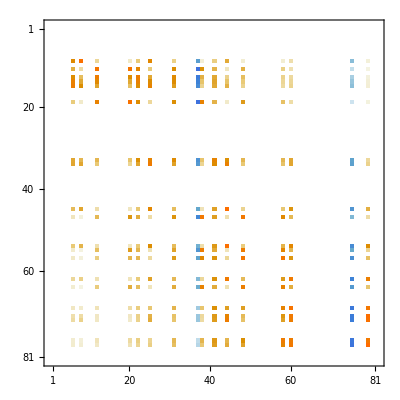

```mathematica
scaledInProbs=((1+attractorScaler)*migrationDimensionalMatrix[[All,#]])&/@sampledAttractors;
replacedMatrix=ReplacePart[migrationDimensionalMatrix//Transpose,(#[[1]]->#[[2]])&/@Transpose[{sampledAttractors,scaledInProbs}]]//Transpose
renormalizedMatrix=(#/Total[#])&/@replacedMatrix
MatrixPlot[Chop[migrationDimensionalMatrix-renormalizedMatrix]]
```

Repellents

```mathematica
{repellentEfficacy,repellentCoverage,repellentDimension}={1,.5,1};
repellentDimensionPositions=Position[cityType,repellentDimension];
sampledRepellents=(repellentDimensionPositions//Flatten//RandomSample)[[1;;Round[repellentCoverage*Length[repellentDimensionPositions]]]]
```

{64,19,57,72,11,55,69,14,13,71}

## Killing

```mathematica
{killingScaler,killingCoverage,killingDimension}={100,.2,3};
killingDimensionPositions=Position[cityType,killingDimension];
sampledKilling=(Position[cityType,killingDimension]//Flatten//RandomSample)[[1;;Round[killingCoverage*Length[killingDimensionPositions]]]]
```

{43,23,36,74}

## Random Walks

```mathematica
paths=Table[
kernel=migrationDimensionalMatrix;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,(RandomSample[Range[kernel//Length]][[1]])->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
sim=RandomFunction[markov,{0,steps}];
path=ToString/@Part[sim["ValueList"],1];
path
,{i,1,chainsNumber}];
paths//Grid
```

Grid[{ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList}]

## Report

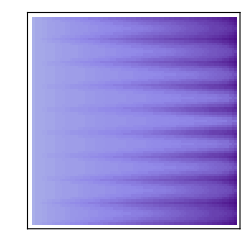
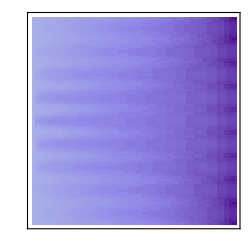
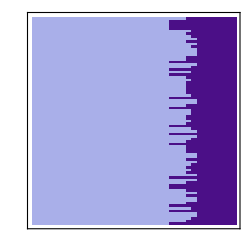
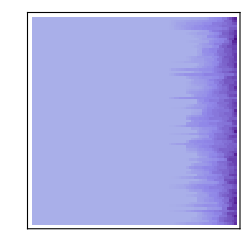
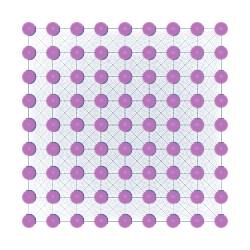
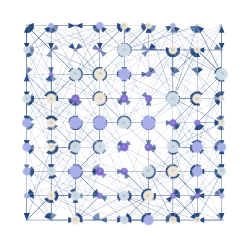
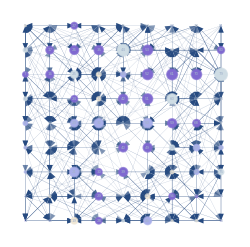
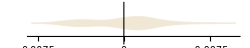
Distances Matrix | Movement Kernel | Dimensions Matrix | Applied Dimensions
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
Pointset | Markov Baseline | Markov Dimensional | Abs[Baseline-Dimensional]
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
 |  | Differences Distribution | Markov Distributions
 |  | -Graphics- | -Graphics-

./images/004ReportGrid.png

```mathematica
Grid[{
Style[#,LineBreakWithin->False]&/@{"Distances Matrix","Movement Kernel","Dimensions Matrix","Applied Dimensions"},
{matrixDistancesPlot,matrixMigrationPlot,matrixPenalizationsPlot,matrixDimensionalPlot},
{"","","",""},
Style[#,LineBreakWithin->False]&/@{"Pointset","Markov Baseline","Markov Dimensional","Abs[Baseline-Dimensional]"},
{originalMap,markovBaseline,markovDimensional,markovDimensionalDifference},
{"","","",""},
Style[#,LineBreakWithin->False]&/@{"","","Differences Distribution","Markov Distributions"},
{"","",distributionOfDifferences,markovDistributions}
}]
Export["./images/"<>StringPadLeft[networkDimension//ToString,3,"0"]<>"ReportGrid.png",%,ImageSize->5000,ImageResolution->1000]
```